```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## Define Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fit[input_,output_,Tscan_]:=Module[{temp=Range[1,Length[Tscan]],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];,{ii,Length[Tscan]}];output=temp;];

store[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];Export["results/"<>temp<>".dat",res];];

storearea[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])( const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];Export["results/"<>temp<>".dat",res];];

import[res_]:=res=Import["results/"<>ToString[res]<>".dat"];
```

## Charmonium s-wave

### Import Data

```mathematica
Tscancorig=Join[Table[i,{i,0.15,0.16,0.001}],Table[i,{i,0.162,0.3,0.003}]]
```

{0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249,0.252,0.255,0.258,0.261,0.264,0.267,0.27,0.273,0.276,0.279,0.282,0.285,0.288,0.291,0.294,0.297,0.3}

```mathematica
Do[ccdata[n]=Import["cc/swccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"spectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscancorig]}];
```

```mathematica
Do[ccdatau[n]=Import["cc/swccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"uspectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscancorig]}];
```

```mathematica
Do[ccdatal[n]=Import["cc/swccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"lspectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscancorig]}];
```

### Fitting

```mathematica
Clear[ccmodelu,ccmodell,ccmodel]
Quiet[fit[ccdata,ccmodel,Tscancorig]];
Quiet[fit[ccdatal,ccmodell,Tscancorig]];
Quiet[fit[ccdatau,ccmodelu,Tscancorig]];
```

### Store Results

```mathematica
Do[If[Length[ccmodel[[i]]]>2,ccmodel[[i]]=ccmodel[[i,;;2]]];
If[Length[ccmodelu[[i]]]>2,ccmodelu[[i]]=ccmodelu[[i,;;2]]];
If[Length[ccmodell[[i]]]>2,ccmodell[[i]]=ccmodell[[i,;;2]]];,{i,Length[ccmodel]}];
```

```mathematica
Clear[wrfitcc,wrfitccl,wrfitccu,gfitcc,gfitccl,gfitccu,areafitcc,areafitccu,areafitccl,cfitcc,cfitccl,cfitccu,dfitcc,dfitccl,dfitccu,sfitcc,sfitccl,sfitccu,s2fitcc,s2fitccl,s2fitccu];
store[wr,wrfitcc,ccmodel];
store[wr,wrfitccl,ccmodell];
store[wr,wrfitccu,ccmodelu];
store[Γ,gfitcc,ccmodel];
store[Γ,gfitccl,ccmodell];
store[Γ,gfitccu,ccmodelu];
store[const,cfitcc,ccmodel];
store[const,cfitccl,ccmodell];
store[const,cfitccu,ccmodelu];
store[δbg,dfitcc,ccmodel];
store[δbg,dfitccl,ccmodell];
store[δbg,dfitccu,ccmodelu];
store[shift,sfitcc,ccmodel];
store[shift,sfitccl,ccmodell];
store[shift,sfitccu,ccmodelu];
store[shift2,s2fitcc,ccmodel];
store[shift2,s2fitccl,ccmodell];
store[shift2,s2fitccu,ccmodelu];
storearea[areafitcc,ccmodel];
storearea[areafitccl,ccmodell];
storearea[areafitccu,ccmodelu];
```

### Display Results

```mathematica
import[wrfitcc];
import[wrfitccl];
import[wrfitccu];
import[gfitcc];
import[gfitccl];
import[gfitccu];
import[cfitcc];
import[cfitccl];
import[cfitccu];
import[dfitcc];
import[dfitccl];
import[dfitccu];
import[sfitcc];
import[sfitccl];
import[sfitccu];
import[s2fitcc];
import[s2fitccl];
import[s2fitccu];
import[areafitcc];
import[areafitccl];
import[areafitccu];
```

```mathematica
cc1Tcut=1;
Do[If[Length[wrfitcc[[-i]]]<2,cc1Tcut=Length[wrfitcc]-i];,{i,Length[wrfitcc]}];
cc1uTcut=1;
Do[If[Length[wrfitccu[[-i]]]<2,cc1uTcut=Length[wrfitccu]-i];,{i,Length[wrfitccl]}];
cc1lTcut=1;Do[If[Length[wrfitccl[[-i]]]<2,cc1lTcut=Length[wrfitccl]-i];,{i,Length[wrfitccu]}];
```

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[ccdatal[i],Joined->True],Plot[BW[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],dfitccl[[i,ii]],cfitccl[[i,ii]],sfitccl[[i,ii]],s2fitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],cfitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[ccdatau[i],Joined->True],Plot[BW[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],dfitccu[[i,ii]],cfitccu[[i,ii]],sfitccu[[i,ii]],s2fitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],cfitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
cccont={3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.701758044310261,3.6590362963255973,3.6196160448966084,3.583057941960285,3.5489997471215924,3.5171399359991113,3.487225338168033,3.459041692083118,3.4328448348117915,3.408694821503098,3.385636846417404,3.363578194413033,3.3424368294912283,3.322139869274786,3.3026223176638405,3.2838260033911766,3.265698687292371,3.2481933077078327,3.2312673392854956,3.2148822483499933,3.199003023017992,3.1835977647233804,3.168637350127192,3.154095119965759,3.1399466184296942,3.126169368591706,3.1127426625685906,3.099647393664894,3.086865895186048,3.074381804177843,3.0621799425923117,3.0502462033554294,3.038567461196708,3.0271314796043938,3.0159268400355783,3.0049428683692474,2.994169575937752,2.9835976023107524,2.9732181665429342,2.9630230178724632,2.9530044013768};
cccontl={3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.7307816791879813,3.698739708227799,3.6683688005341324,3.639517533974076,3.612052845800916,3.585857293752711,3.560826796256764,3.536868756562935,3.5139004960437386,3.491847943523757,3.470644523536246,3.4502302060802545,3.4305507241781674,3.4115568716559106,3.3932039183081444,3.375451110944204,3.358261217583014,3.341600161442533,3.3254366778242237,3.309742025225839,3.2944897354070544,3.2796553782840547,3.265216376830746,3.2511518188927626,3.2374423129173984,3.224069841349274,3.211017642916522,3.1982700999651126,3.185812642831631,3.1736316544043746,3.1617144032873044};
cccontu={3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.7314782670933067,3.710507093943211,3.690397562453125,3.6710886578917625,3.6346569136085773,3.5847874788364775,3.5397529008546043,3.4987535608775717,3.46116204469073,3.4264787031113695,3.3943003544048773,3.3642977986677383,3.336199371862016,3.309778725468078,3.284845611469781,3.261238842932823,3.238820851521168,3.217473433225475,3.1973572919282236,3.178514814156032,3.16037650279606,3.142887954333365,3.1260005530148907,3.1096707002465855,3.0938591664534365,3.078530541623156,3.063652767931,3.0491967404147484,3.0351359641507702,3.0214462603415906,3.008105510171779,2.9950934299747627,2.982391384137269,2.9699822107884337,2.9578500749920846,2.945980341295423,2.9343594535635162,2.922974838349634,2.9118148113801365,2.9008684980107886,2.8901257633545385,2.879577145053365,2.8692138000595273,2.859027449226631,2.8490103344924274,2.8391551746268875,2.8294551292347663,2.8199037638907916,2.8104950200919028,2.8012231851775447,2.7920828704287475};
```

```mathematica
Export["plots/cc_Econt.dat",Transpose[{Tscancorig,cccont,cccontl,cccontu}]]
```

plots/cc_Econt.dat

```mathematica
ccbind=cccont-wrfitcc;
ccbindu=cccontu-wrfitccu;
ccbindl=cccontl-wrfitccl;
```

```mathematica
Do[If[(ccbind-gfitcc)[[i,1]]>0,cc1Tmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbind-gfitcc)[[i,2]]>0,cc2Tmelt=i,cc2Tmelt=1],{i,1,cc1Tcut}];
Do[If[(ccbindl-gfitccl)[[i,1]]>0,cc1lTmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbindl-gfitccl)[[i,2]]>0,cc2lTmelt=i,cc2lTmelt=1],{i,1,cc1lTcut}];
Do[If[(ccbindu-gfitccu)[[i,1]]>0,cc1uTmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbindu-gfitccu)[[i,2]]>0,cc2uTmelt=i,cc2uTmelt=1],{i,1,cc1uTcut}];
```

```mathematica
N[{Tscancorig[[cc1lTmelt]],Tscancorig[[cc1Tmelt]],Tscancorig[[cc1uTmelt]]}/0.155]
```

{1.93548,1.72258,1.49032}

```mathematica
N[{Tscancorig[[cc2lTmelt]],Tscancorig[[cc2Tmelt]],Tscancorig[[cc2uTmelt]]}/0.155]
```

{0.967742,0.967742,0.967742}

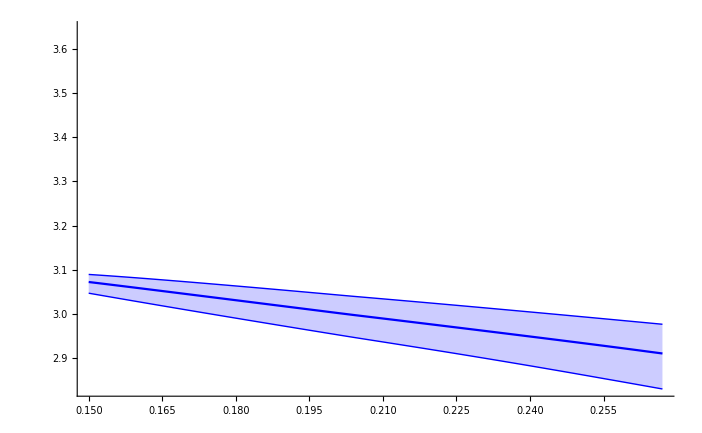

```mathematica
ListPlot[{Transpose[{Tscancorig[[;;cc1Tmelt]],wrfitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc1Tmelt]],wrfitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc1Tmelt]],wrfitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],wrfitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],wrfitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],wrfitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

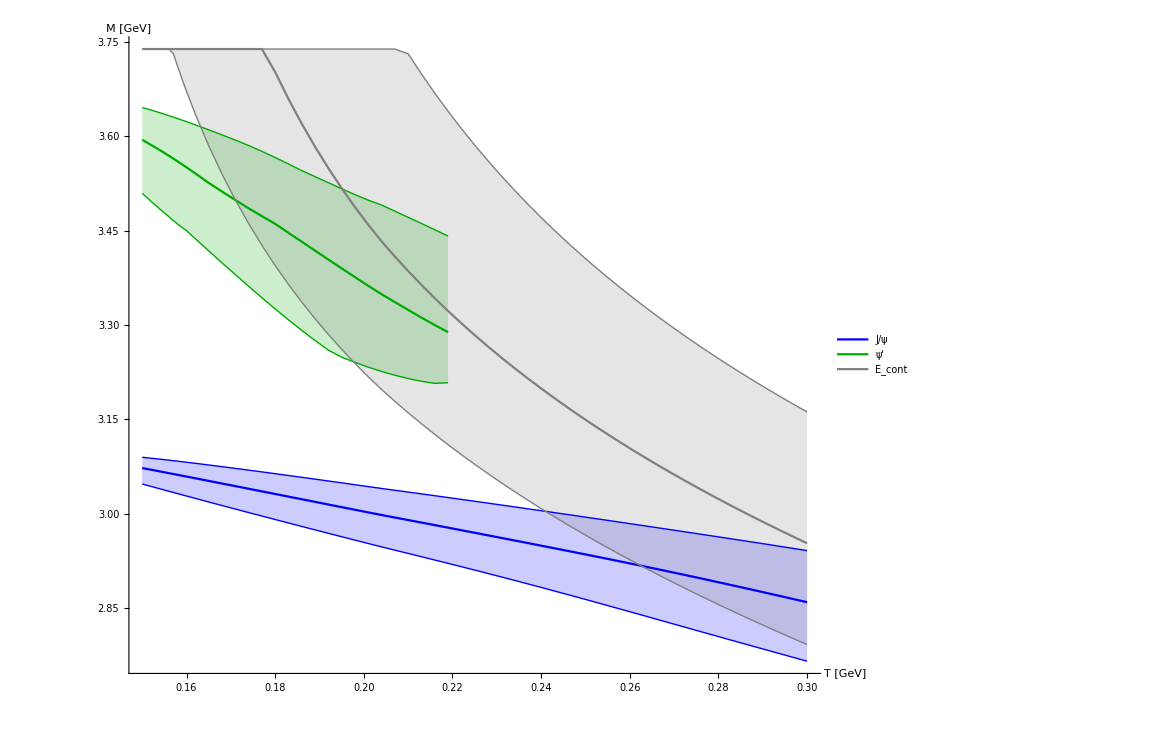

```mathematica
ListPlot[{Transpose[{Tscancorig,wrfitcc[[All,1]]}],Transpose[{Tscancorig,wrfitccl[[All,1]]}],Transpose[{Tscancorig,wrfitccu[[All,1]]}],Transpose[{Tscancorig[[;;cc1uTcut-1]],wrfitcc[[;;cc1uTcut-1,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-1]],wrfitccl[[;;cc1uTcut-1,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-1]],wrfitccu[[;;cc1uTcut-1,2]]}],Transpose[{Tscancorig,cccont}],Transpose[{Tscancorig,cccontu}],Transpose[{Tscancorig,cccontl}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Darker[Green],{Darker[Green],Thin},{Darker[Green],Thin},Gray,{Gray,Thin},{Gray,Thin}},Joined->True,AxesLabel->{Style["T [GeV]",25,Black],Style["M [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"],None,None,Style["E_cont",25,"Helvetica"]}],{0.8,0.8}]]
```

```mathematica
Export["plots/Jpsi_mass.dat",Transpose[{Tscancorig,wrfitcc[[All,1]],wrfitccl[[All,1]],wrfitccu[[All,1]]}]]
```

plots/Jpsi_mass.dat

```mathematica
Export["plots/psip_mass.dat",Transpose[{Tscancorig[[;;cc1uTcut-1]],wrfitcc[[;;cc1uTcut-1,2]],wrfitccl[[;;cc1uTcut-1,2]],wrfitccu[[;;cc1uTcut-1,2]]}]]
```

plots/psip_mass.dat

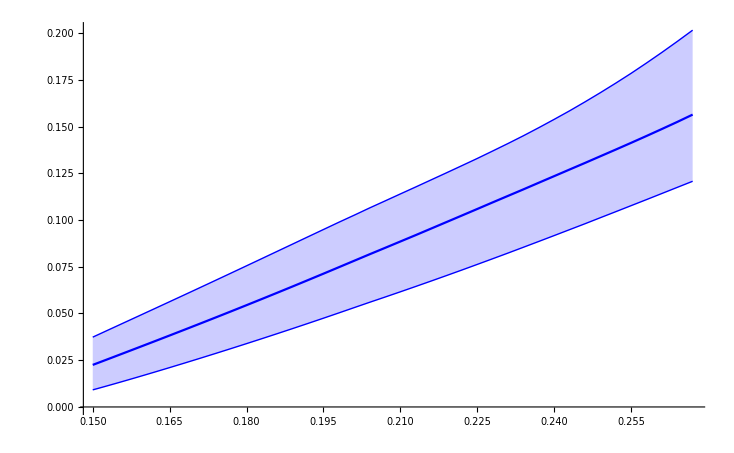

```mathematica
ListPlot[{Transpose[{Tscancorig[[;;cc1Tmelt]],gfitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc1Tmelt]],gfitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc1Tmelt]],gfitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],gfitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],gfitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],gfitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

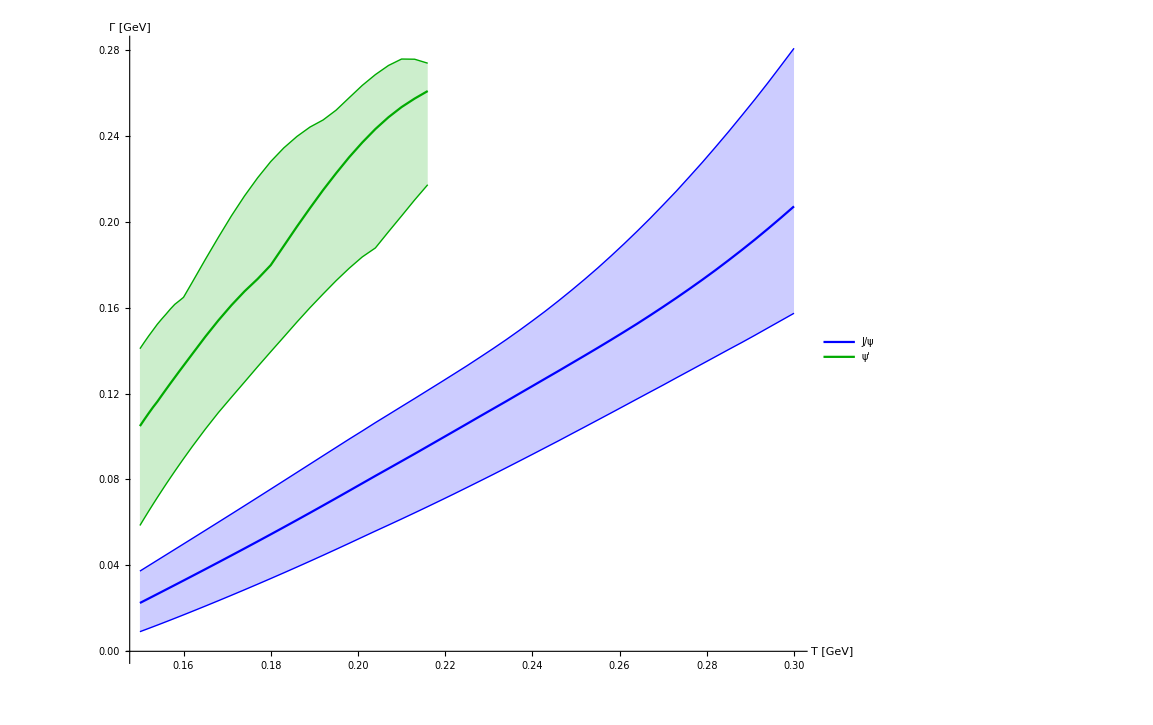

```mathematica
ListPlot[{Transpose[{Tscancorig[[;;]],gfitcc[[;;,1]]}],Transpose[{Tscancorig[[;;]],gfitccl[[;;,1]]}],Transpose[{Tscancorig[[;;]],gfitccu[[;;,1]]}],Transpose[{Tscancorig[[;;cc1uTcut-2]],gfitcc[[;;cc1uTcut-2,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-2]],gfitccl[[;;cc1uTcut-2,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-2]],gfitccu[[;;cc1uTcut-2,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Darker[Green],{Darker[Green],Thin},{Darker[Green],Thin},Gray,{Gray,Thin},{Gray,Thin}},Joined->True,AxesLabel->{Style["T [GeV]",25,Black],Style["Γ [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"]}],{0.8,0.2}]]
```

```mathematica
Export["plots/Jpsi_width.dat",Transpose[{Tscancorig,gfitcc[[All,1]],gfitccl[[All,1]],gfitccu[[All,1]]}]]
```

plots/Jpsi_width.dat

```mathematica
Export["plots/psip_width.dat",Transpose[{Tscancorig[[;;cc1uTcut-2]],gfitcc[[;;cc1uTcut-2,2]],gfitccl[[;;cc1uTcut-2,2]],gfitccu[[;;cc1uTcut-2,2]]}]]
```

plots/psip_width.dat

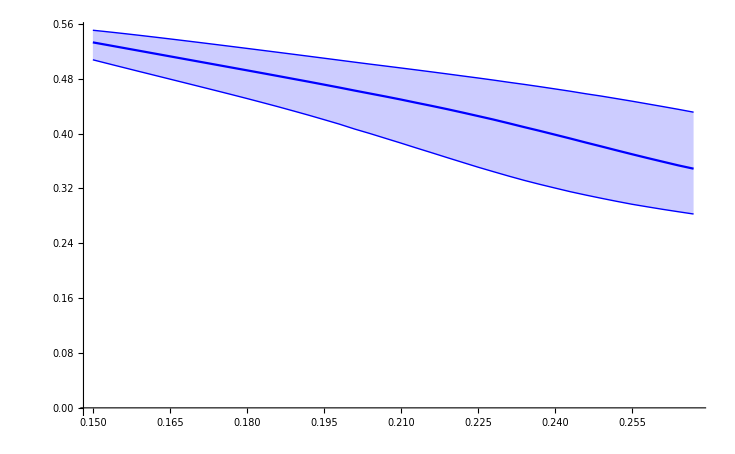

```mathematica
ListPlot[{Transpose[{Tscancorig[[;;cc1Tmelt]],areafitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc1Tmelt]],areafitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc1Tmelt]],areafitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],areafitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],areafitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],areafitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

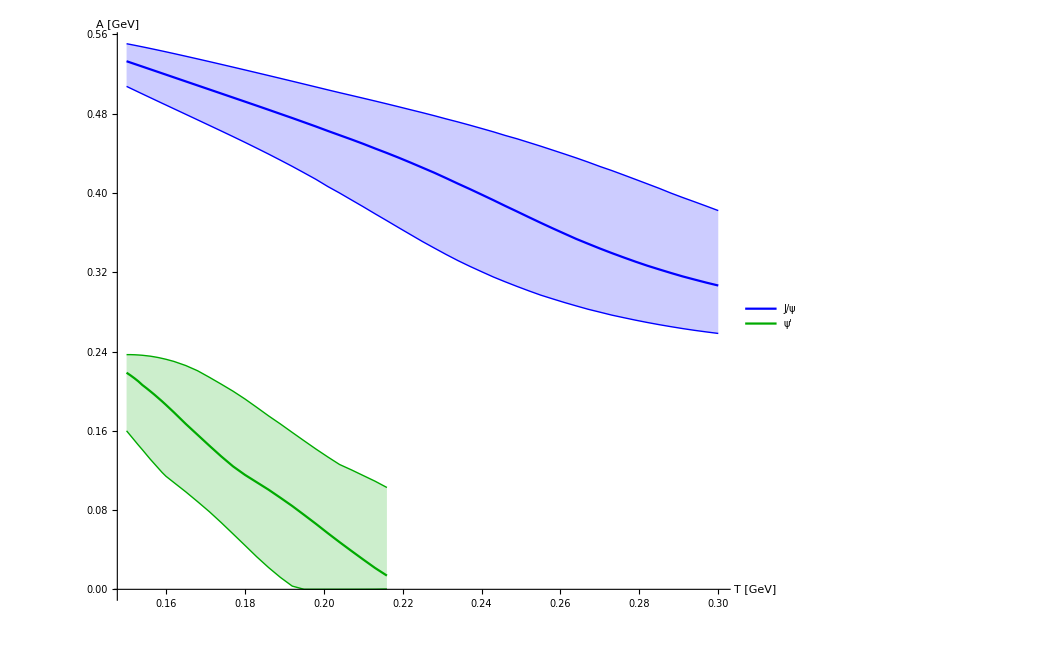

```mathematica
ListPlot[{Transpose[{Tscancorig[[;;]],areafitcc[[;;,1]]}],Transpose[{Tscancorig[[;;]],areafitccl[[;;,1]]}],Transpose[{Tscancorig[[;;]],areafitccu[[;;,1]]}],Transpose[{Tscancorig[[;;cc1uTcut-2]],areafitcc[[;;cc1uTcut-2,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-2]],areafitccl[[;;cc1uTcut-2,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-2]],areafitccu[[;;cc1uTcut-2,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Darker[Green],{Darker[Green],Thin},{Darker[Green],Thin},Gray,{Gray,Thin},{Gray,Thin}},Joined->True,AxesLabel->{Style["T [GeV]",25,Black],Style["A [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"]}],{0.8,0.2}]]
```

```mathematica
Export["plots/Jpsi_area.dat",Transpose[{Tscancorig,areafitcc[[All,1]],areafitccl[[All,1]],areafitccu[[All,1]]}]]
```

plots/Jpsi_area.dat

```mathematica
Export["plots/psip_area.dat",Transpose[{Tscancorig[[;;cc1uTcut-2]],areafitcc[[;;cc1uTcut-2,2]],areafitccl[[;;cc1uTcut-2,2]],areafitccu[[;;cc1uTcut-2,2]]}]]
```

plots/psip_area.dat

## Charmonium p-wave

### Import Data

```mathematica
Tscancorig=Join[Table[i,{i,0.15,0.16,0.001}],Table[i,{i,0.162,0.3,0.003}]]
```

{0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249,0.252,0.255,0.258,0.261,0.264,0.267,0.27,0.273,0.276,0.279,0.282,0.285,0.288,0.291,0.294,0.297,0.3}

```mathematica
Do[ccdata[n]=Import["cc/pwccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"spectra.dat"]/.{a_,b_}:>{a,b/a^2};,{n,Length[Tscancorig]}];
```

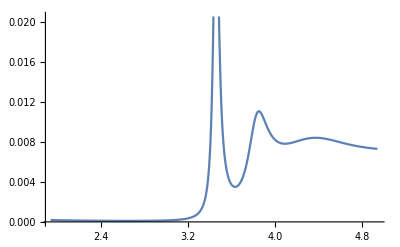

```mathematica
Block[{n=1},ListPlot[ccdata[n],Joined->True]]
```

```mathematica
Do[ccdatau[n]=Import["cc/pwccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"uspectra.dat"]/.{a_,b_}:>{a,b/a^2};,{n,Length[Tscancorig]}];
```

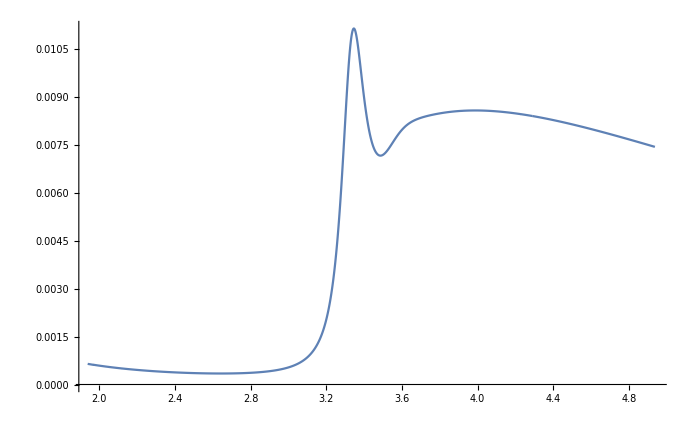

```mathematica
Block[{n=14},ListPlot[ccdatau[n],Joined->True]]
```

```mathematica
Do[ccdatal[n]=Import["cc/pwccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"lspectra.dat"]/.{a_,b_}:>{a,b/a^2};,{n,Length[Tscancorig]}];
```

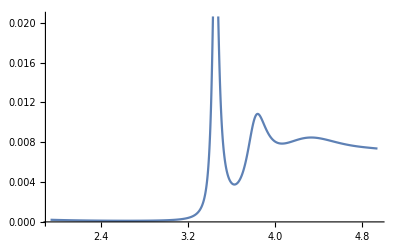

```mathematica
Block[{n=3},ListPlot[ccdata[n],Joined->True]]
```

### Fitting

```mathematica
Clear[ccmodelu,ccmodell,ccmodel]
Quiet[fit[ccdata,ccmodel,Tscancorig]];
Quiet[fit[ccdatal,ccmodell,Tscancorig]];
Quiet[fit[ccdatau,ccmodelu,Tscancorig]];
```

### Store Results

```mathematica
Do[If[Length[ccmodel[[i]]]>2,ccmodel[[i]]=ccmodel[[i,;;2]]];
If[Length[ccmodelu[[i]]]>2,ccmodelu[[i]]=ccmodelu[[i,;;2]]];
If[Length[ccmodell[[i]]]>2,ccmodell[[i]]=ccmodell[[i,;;2]]];,{i,Length[ccmodel]}];
```

```mathematica
Clear[wrfitccp,wrfitccpl,wrfitccpu,gfitccp,gfitccpl,gfitccpu,areafitccp,areafitccpu,areafitccpl,cfitccp,cfitccpl,cfitccpu,dfitccp,dfitccpl,dfitccpu,sfitccp,sfitccpl,sfitccpu,s2fitccp,s2fitccpl,s2fitccpu];
```

```mathematica
store[wr,wrfitccp,ccmodel];
store[wr,wrfitccpl,ccmodell];
store[wr,wrfitccpu,ccmodelu];
store[Γ,gfitccp,ccmodel];
store[Γ,gfitccpl,ccmodell];
store[Γ,gfitccpu,ccmodelu];
store[const,cfitccp,ccmodel];
store[const,cfitccpl,ccmodell];
store[const,cfitccpu,ccmodelu];
store[δbg,dfitccp,ccmodel];
store[δbg,dfitccpl,ccmodell];
store[δbg,dfitccpu,ccmodelu];
store[shift,sfitccp,ccmodel];
store[shift,sfitccpl,ccmodell];
store[shift,sfitccpu,ccmodelu];
store[shift2,s2fitccp,ccmodel];
store[shift2,s2fitccpl,ccmodell];
store[shift2,s2fitccpu,ccmodelu];
storearea[areafitccp,ccmodel];
storearea[areafitccpl,ccmodell];
storearea[areafitccpu,ccmodelu];
```

### Display Results

```mathematica
import[wrfitccp];
import[wrfitccpl];
import[wrfitccpu];
import[gfitccp];
import[gfitccpl];
import[gfitccpu];
import[cfitccp];
import[cfitccpl];
import[cfitccpu];
import[dfitccp];
import[dfitccpl];
import[dfitccpu];
import[sfitccp];
import[sfitccpl];
import[sfitccpu];
import[s2fitccp];
import[s2fitccpl];
import[s2fitccpu];
import[areafitccp];
import[areafitccpl];
import[areafitccpu];
```

```mathematica
Length[wrfitccp]
```

57

```mathematica
cc1Tcut=1;
Do[If[Length[wrfitccp[[-i]]]<2,cc1Tcut=Length[wrfitccp]-i];,{i,Length[wrfitccp]}];
cc1uTcut=1;
Do[If[Length[wrfitccpu[[-i]]]<2,cc1uTcut=Length[wrfitccpu]-i];,{i,Length[wrfitccpl]}];
cc1lTcut=1;Do[If[Length[wrfitccpl[[-i]]]<2,cc1lTcut=Length[wrfitccpl]-i];,{i,Length[wrfitccpu]}];
```

```mathematica
fitONE[input_]:=Module[{maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxis,mins,hwhmi,bad},
maxx=Max[input[[All,1]]];
minx=Min[input[[All,1]]];
maxy=Max[input[[All,2]]];
maxyx=input[[Position[input,Max[input[[All,2]]]][[1,1]],1]];
maxyi=Position[input[[All,1]],maxyx][[1,1]];
maxxy=input[[Position[input,Max[input[[All,1]]]][[1,1]],2]];
inter=Interpolation[input,InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[[All,1]],Nearest[input[[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[[maxxis[[i]]-30,2]]>input[[maxxis[[i]],2]],input[[maxxis[[i]]+30,2]]>input[[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[[All,2]],Min[input[[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input]]];,
hwhmi=Position[input,Nearest[input[[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input],maxyi+3(maxyi-hwhmi),Length[input]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input,Nearest[input[[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];];
```

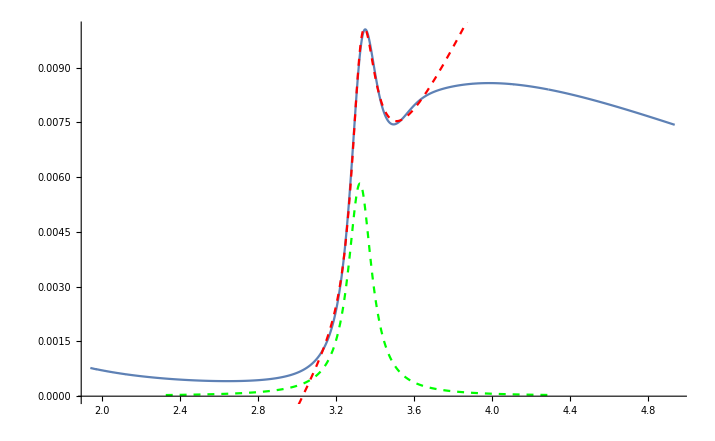

```mathematica
Block[{i=23,ii=1},Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitccp[[i,ii]],gfitccp[[i,ii]],dfitccp[[i,ii]],cfitccp[[i,ii]],sfitccp[[i,ii]],s2fitccp[[i,ii]]],{x,0.7wrfitccp[[i,ii]],1.3wrfitccp[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccp[[i,ii]],gfitccp[[i,ii]],cfitccp[[i,ii]]],{x,0.7wrfitccp[[i,ii]],1.3wrfitccp[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

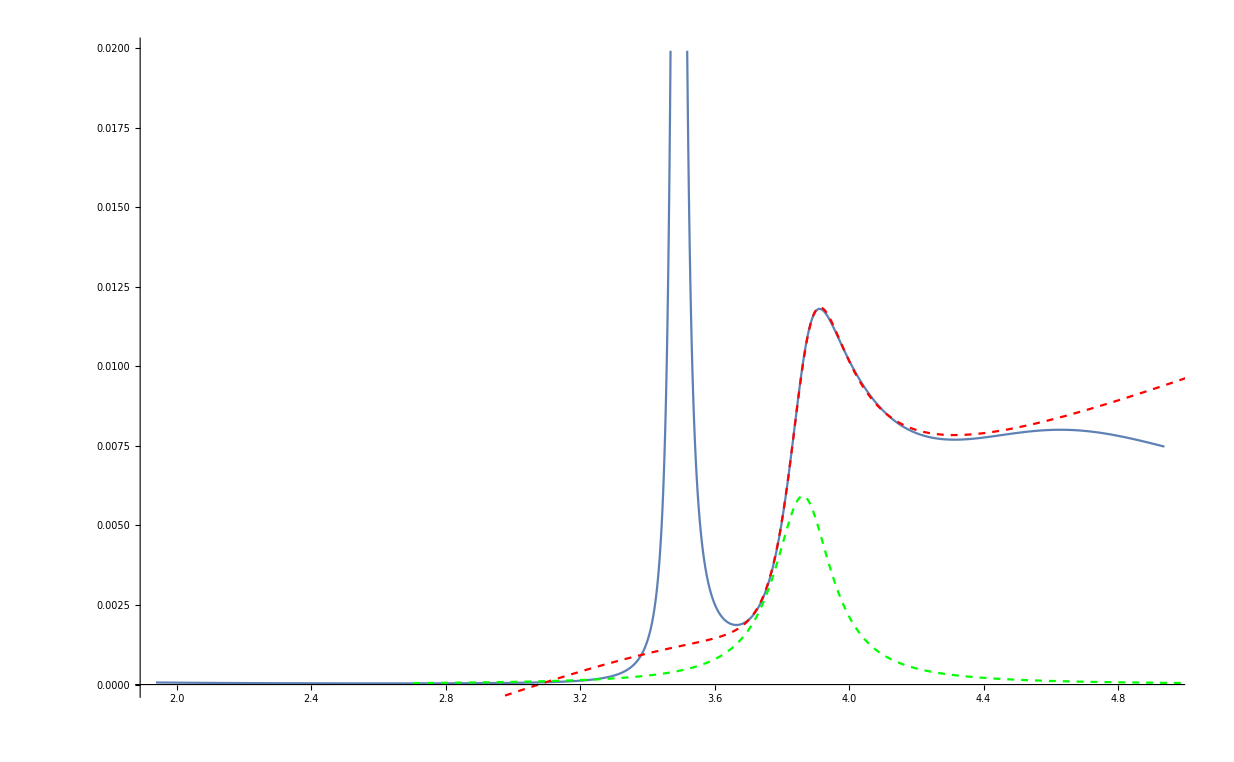

```mathematica
Block[{i=1,ii=2},Show[{ListPlot[ccdatal[i],Joined->True],Plot[BW[x,wrfitccpl[[i,ii]],gfitccpl[[i,ii]],dfitccpl[[i,ii]],cfitccpl[[i,ii]],sfitccpl[[i,ii]],s2fitccpl[[i,ii]]],{x,0.7wrfitccpl[[i,ii]],1.3wrfitccpl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccpl[[i,ii]],gfitccpl[[i,ii]],cfitccpl[[i,ii]]],{x,0.7wrfitccpl[[i,ii]],1.3wrfitccpl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

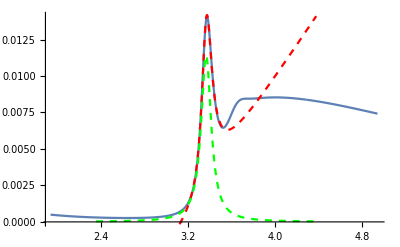

```mathematica
Block[{i=10,ii=1},Show[{ListPlot[ccdatau[i],Joined->True],Plot[BW[x,wrfitccpu[[i,ii]],gfitccpu[[i,ii]],dfitccpu[[i,ii]],cfitccpu[[i,ii]],sfitccpu[[i,ii]],s2fitccpu[[i,ii]]],{x,0.7wrfitccpu[[i,ii]],1.3wrfitccpu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccpu[[i,ii]],gfitccpu[[i,ii]],cfitccpu[[i,ii]]],{x,0.7wrfitccpu[[i,ii]],1.3wrfitccpu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
cccont={3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.701758044310261,3.6590362963255973,3.6196160448966084,3.583057941960285,3.5489997471215924,3.5171399359991113,3.487225338168033,3.459041692083118,3.4328448348117915,3.408694821503098,3.385636846417404,3.363578194413033,3.3424368294912283,3.322139869274786,3.3026223176638405,3.2838260033911766,3.265698687292371,3.2481933077078327,3.2312673392854956,3.2148822483499933,3.199003023017992,3.1835977647233804,3.168637350127192,3.154095119965759,3.1399466184296942,3.126169368591706,3.1127426625685906,3.099647393664894,3.086865895186048,3.074381804177843,3.0621799425923117,3.0502462033554294,3.038567461196708,3.0271314796043938,3.0159268400355783,3.0049428683692474,2.994169575937752,2.9835976023107524,2.9732181665429342,2.9630230178724632,2.9530044013768};
cccontl={3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.7307816791879813,3.698739708227799,3.6683688005341324,3.639517533974076,3.612052845800916,3.585857293752711,3.560826796256764,3.536868756562935,3.5139004960437386,3.491847943523757,3.470644523536246,3.4502302060802545,3.4305507241781674,3.4115568716559106,3.3932039183081444,3.375451110944204,3.358261217583014,3.341600161442533,3.3254366778242237,3.309742025225839,3.2944897354070544,3.2796553782840547,3.265216376830746,3.2511518188927626,3.2374423129173984,3.224069841349274,3.211017642916522,3.1982700999651126,3.185812642831631,3.1736316544043746,3.1617144032873044};
cccontu={3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.7314782670933067,3.710507093943211,3.690397562453125,3.6710886578917625,3.6346569136085773,3.5847874788364775,3.5397529008546043,3.4987535608775717,3.46116204469073,3.4264787031113695,3.3943003544048773,3.3642977986677383,3.336199371862016,3.309778725468078,3.284845611469781,3.261238842932823,3.238820851521168,3.217473433225475,3.1973572919282236,3.178514814156032,3.16037650279606,3.142887954333365,3.1260005530148907,3.1096707002465855,3.0938591664534365,3.078530541623156,3.063652767931,3.0491967404147484,3.0351359641507702,3.0214462603415906,3.008105510171779,2.9950934299747627,2.982391384137269,2.9699822107884337,2.9578500749920846,2.945980341295423,2.9343594535635162,2.922974838349634,2.9118148113801365,2.9008684980107886,2.8901257633545385,2.879577145053365,2.8692138000595273,2.859027449226631,2.8490103344924274,2.8391551746268875,2.8294551292347663,2.8199037638907916,2.8104950200919028,2.8012231851775447,2.7920828704287475};
```

```mathematica
ccbind=cccont[[;;-2]]-wrfitccp;
ccbindu=cccontu-wrfitccpu;
ccbindl=cccontl-wrfitccpl;
```

```mathematica
Do[If[(ccbind-gfitccp)[[i,1]]>0,cc1Tmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbind-gfitccp)[[i,2]]>0,cc2Tmelt=i,cc2Tmelt=1],{i,1,cc1Tcut}];
Do[If[(ccbindl-gfitccpl)[[i,1]]>0,cc1lTmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbindl-gfitccpl)[[i,2]]>0,cc2lTmelt=i,cc2lTmelt=1],{i,1,cc1lTcut}];
Do[If[(ccbindu-gfitccpu)[[i,1]]>0,cc1uTmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbindu-gfitccpu)[[i,2]]>0,cc2uTmelt=i,cc2uTmelt=1],{i,1,cc1uTcut}];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
N[{Tscancorig[[cc1lTmelt]],Tscancorig[[cc1Tmelt]],Tscancorig[[cc1uTmelt]]}/0.155]
```

{1.49032,1.27742,1.12258}

```mathematica
N[{Tscancorig[[cc2lTmelt]],Tscancorig[[cc2Tmelt]],Tscancorig[[cc2uTmelt]]}/0.155]
```

{0.967742,0.967742,0.967742}

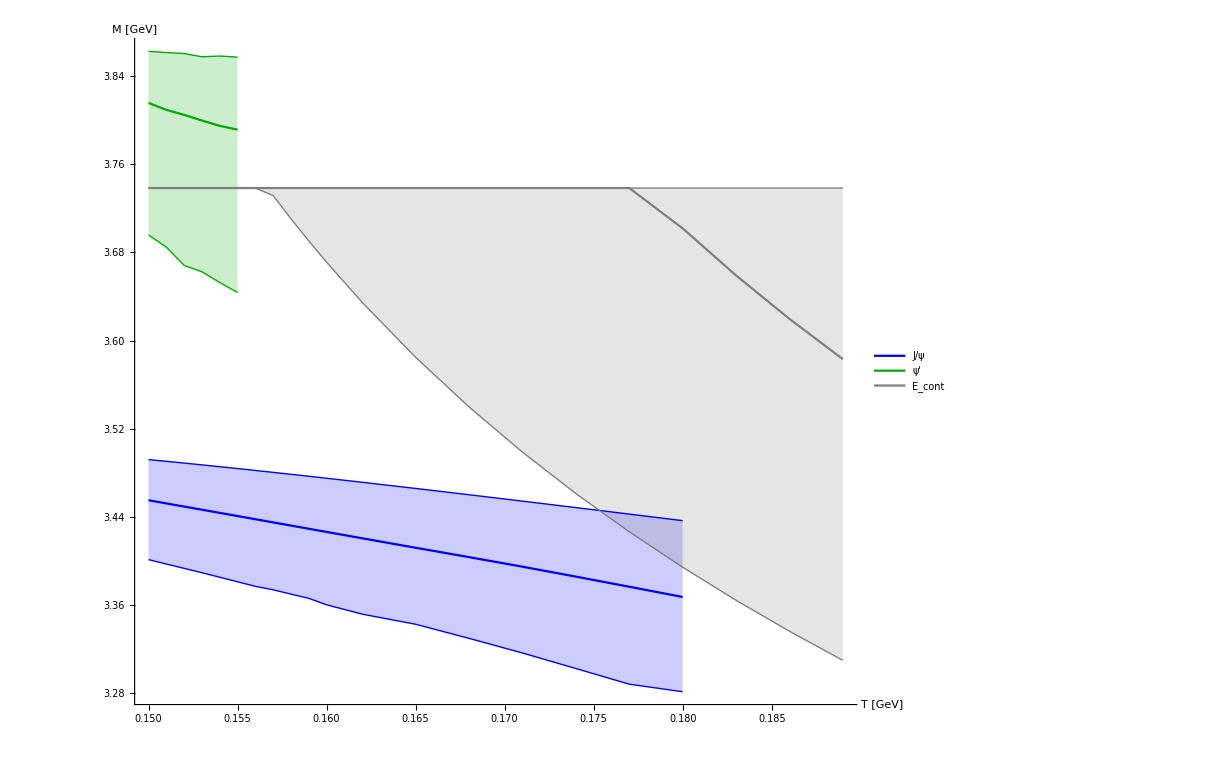

```mathematica
ListPlot[{Transpose[{Tscancorig[[;;cc1uTmelt+2]],wrfitccp[[;;cc1uTmelt+2,1]]}],Transpose[{Tscancorig[[;;cc1uTmelt+2]],wrfitccpl[[;;cc1uTmelt+2,1]]}],Transpose[{Tscancorig[[;;cc1uTmelt+2]],wrfitccpu[[;;cc1uTmelt+2,1]]}],Transpose[{Tscancorig[[;;cc1uTcut-1]],wrfitccp[[;;cc1uTcut-1,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-1]],wrfitccpl[[;;cc1uTcut-1,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-1]],wrfitccpu[[;;cc1uTcut-1,2]]}],Transpose[{Tscancorig[[;;cc1uTmelt+5]],cccont[[;;cc1uTmelt+5]]}],Transpose[{Tscancorig[[;;cc1uTmelt+5]],cccontu[[;;cc1uTmelt+5]]}],Transpose[{Tscancorig[[;;cc1uTmelt+5]],cccontl[[;;cc1uTmelt+5]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Darker[Green],{Darker[Green],Thin},{Darker[Green],Thin},Gray,{Gray,Thin},{Gray,Thin}},Joined->True,AxesLabel->{Style["T [GeV]",25,Black],Style["M [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"],None,None,Style["E_cont",25,"Helvetica"]},LegendLayout->"Row"],{0.5,0.9}]]
```

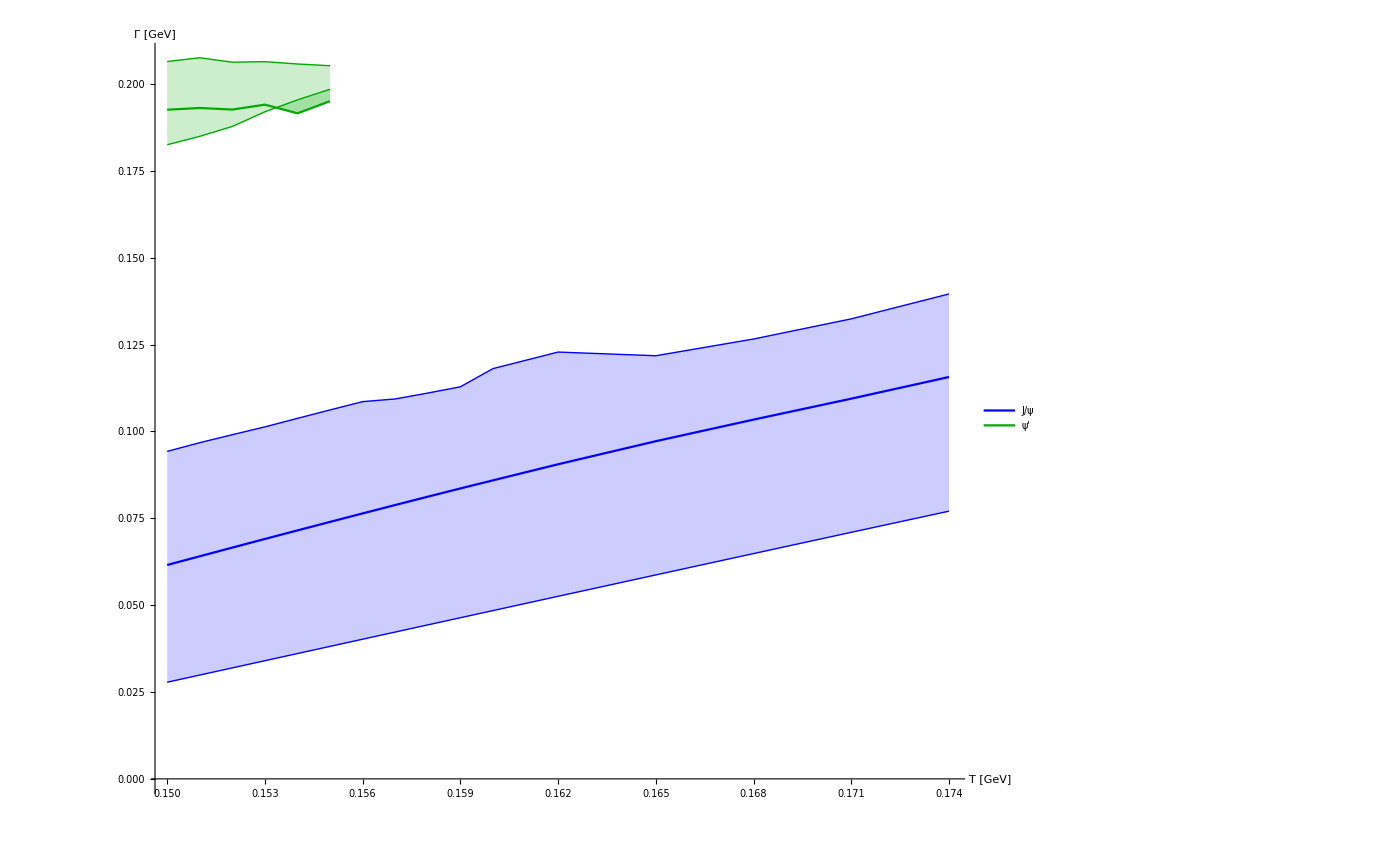

```mathematica
ListPlot[{Transpose[{Tscancorig[[;;cc1uTmelt]],gfitccp[[;;cc1uTmelt,1]]}],Transpose[{Tscancorig[[;;cc1uTmelt]],gfitccpl[[;;cc1uTmelt,1]]}],Transpose[{Tscancorig[[;;cc1uTmelt]],gfitccpu[[;;cc1uTmelt,1]]}],Transpose[{Tscancorig[[;;cc1uTcut-1]],gfitccp[[;;cc1uTcut-1,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-1]],gfitccpl[[;;cc1uTcut-1,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-1]],gfitccpu[[;;cc1uTcut-1,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Darker[Green],{Darker[Green],Thin},{Darker[Green],Thin}},Joined->True,AxesLabel->{Style["T [GeV]",25,Black],Style["Γ [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"]}],{0.6,0.75}]]
```

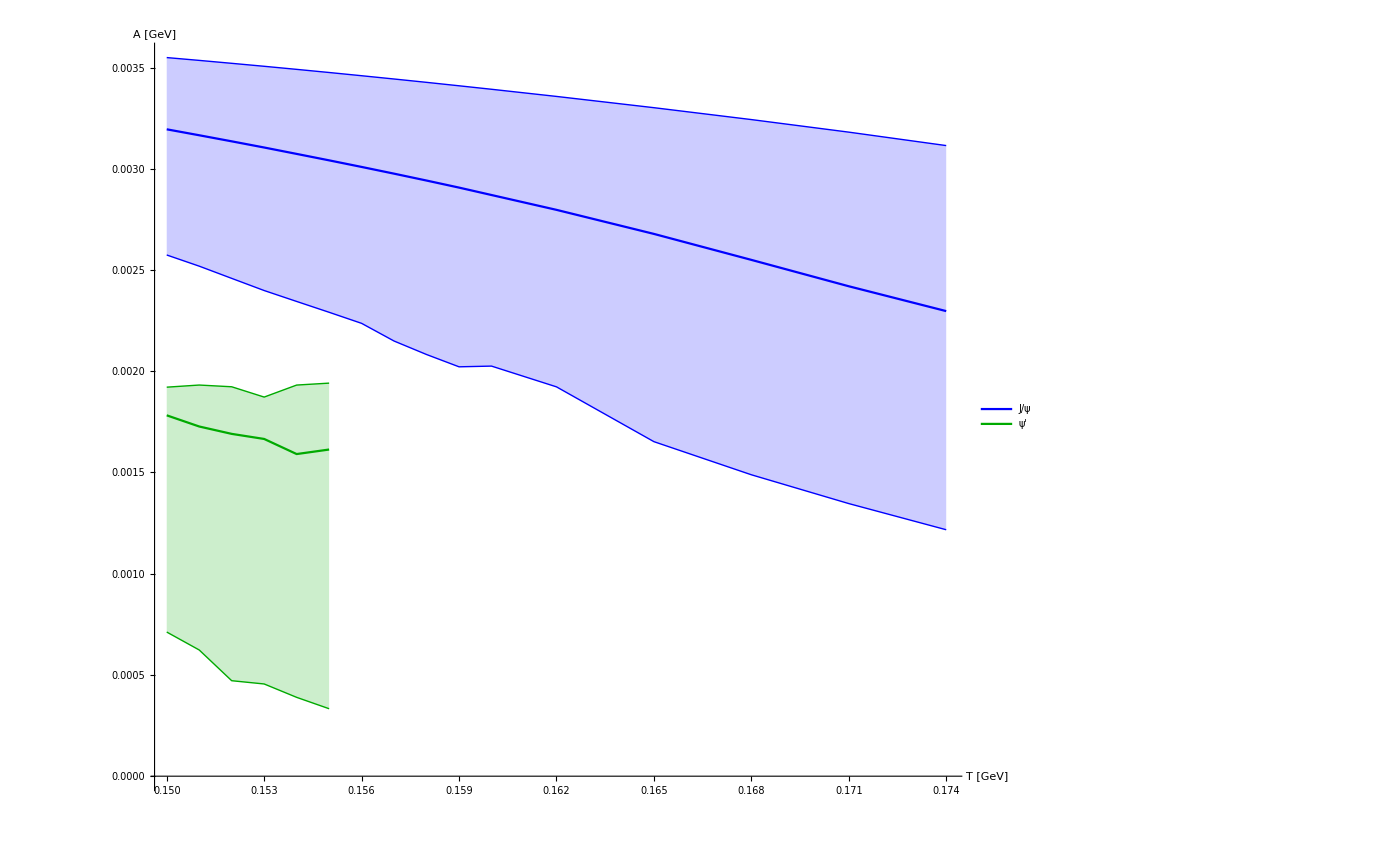

```mathematica
ListPlot[{Transpose[{Tscancorig[[;;cc1uTmelt]],areafitccp[[;;cc1uTmelt,1]]}],Transpose[{Tscancorig[[;;cc1uTmelt]],areafitccpl[[;;cc1uTmelt,1]]}],Transpose[{Tscancorig[[;;cc1uTmelt]],areafitccpu[[;;cc1uTmelt,1]]}],Transpose[{Tscancorig[[;;cc1uTcut-1]],areafitccp[[;;cc1uTcut-1,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-1]],areafitccpl[[;;cc1uTcut-1,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-1]],areafitccpu[[;;cc1uTcut-1,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Darker[Green],{Darker[Green],Thin},{Darker[Green],Thin}},Joined->True,AxesLabel->{Style["T [GeV]",25,Black],Style["A [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"]}],{0.8,0.2}]]
```

## Bottomonium s-wave

```mathematica
Tscanborig=Table[i,{i,0.15,0.6,0.005}]
```

{0.15,0.155,0.16,0.165,0.17,0.175,0.18,0.185,0.19,0.195,0.2,0.205,0.21,0.215,0.22,0.225,0.23,0.235,0.24,0.245,0.25,0.255,0.26,0.265,0.27,0.275,0.28,0.285,0.29,0.295,0.3,0.305,0.31,0.315,0.32,0.325,0.33,0.335,0.34,0.345,0.35,0.355,0.36,0.365,0.37,0.375,0.38,0.385,0.39,0.395,0.4,0.405,0.41,0.415,0.42,0.425,0.43,0.435,0.44,0.445,0.45,0.455,0.46,0.465,0.47,0.475,0.48,0.485,0.49,0.495,0.5,0.505,0.51,0.515,0.52,0.525,0.53,0.535,0.54,0.545,0.55,0.555,0.56,0.565,0.57,0.575,0.58,0.585,0.59,0.595,0.6}

```mathematica
Do[bbdata[n]=Import["bb/swbbT"<>ToString[Round[1000 Tscanborig[[n]]]]<>"spectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscanborig]}];
```

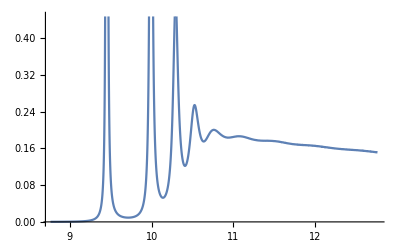

```mathematica
Block[{n=1},ListPlot[bbdata[n],Joined->True]]
```

```mathematica
Do[bbdatal[n]=Import["bb/swbbT"<>ToString[Round[1000 Tscanborig[[n]]]]<>"lspectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscanborig]}];
```

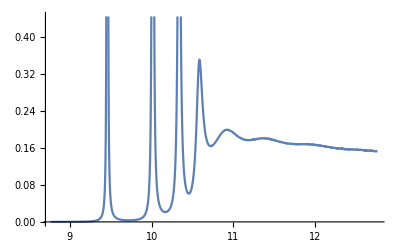

```mathematica
Block[{n=1},ListPlot[bbdatal[n],Joined->True]]
```

```mathematica
Do[bbdatau[n]=Import["bb/swbbT"<>ToString[Round[1000 Tscanborig[[n]]]]<>"uspectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscanborig]}];
```

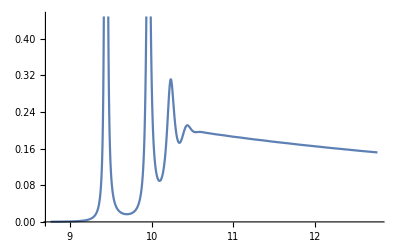

```mathematica
Block[{n=1},ListPlot[bbdatau[n],Joined->True]]
```

### Fitting

```mathematica
Clear[bbmodel,bbmodelu,bbmodell]
fit[bbdata,bbmodel,Tscanborig];
fit[bbdatau,bbmodelu,Tscanborig];
fit[bbdatal,bbmodell,Tscanborig];
```

### Store Results

```mathematica
Do[If[Length[bbmodel[[i]]]>4,bbmodel[[i]]=bbmodel[[i,;;4]]];If[Length[bbmodelu[[i]]]>4,bbmodelu[[i]]=bbmodelu[[i,;;4]]];If[Length[bbmodell[[i]]]>4,bbmodell[[i]]=bbmodell[[i,;;4]]];,{i,Length[bbmodel]}];
```

```mathematica
Clear[wrfitbb,wrfitbbl,wrfitbbu,gfitbb,gfitbbl,gfitbbu,areafitbb,areafitbbu,areafitbbl,cfitbb,cfitbbl,cfitbbu,dfitbb,dfitbbl,dfitbbu,sfitbb,sfitbbl,sfitbbu,s2fitbb,s2fitbbl,s2fitbbu];
store[wr,wrfitbb,bbmodel];
store[wr,wrfitbbl,bbmodell];
store[wr,wrfitbbu,bbmodelu];
store[Γ,gfitbb,bbmodel];
store[Γ,gfitbbl,bbmodell];
store[Γ,gfitbbu,bbmodelu];
store[const,cfitbb,bbmodel];
store[const,cfitbbl,bbmodell];
store[const,cfitbbu,bbmodelu];
store[δbg,dfitbb,bbmodel];
store[δbg,dfitbbl,bbmodell];
store[δbg,dfitbbu,bbmodelu];
store[shift,sfitbb,bbmodel];
store[shift,sfitbbl,bbmodell];
store[shift,sfitbbu,bbmodelu];
store[shift2,s2fitbb,bbmodel];
store[shift2,s2fitbbl,bbmodell];
store[shift2,s2fitbbu,bbmodelu];
storearea[areafitbb,bbmodel];
storearea[areafitbbl,bbmodell];
storearea[areafitbbu,bbmodelu];
```

### Display Results

```mathematica
import[wrfitbb];
import[wrfitbbl];
import[wrfitbbu];
import[gfitbb];
import[gfitbbl];
import[gfitbbu];
import[cfitbb];
import[cfitbbl];
import[cfitbbu];
import[dfitbb];
import[dfitbbl];
import[dfitbbu];
import[sfitbb];
import[sfitbbl];
import[sfitbbu];
import[s2fitbb];
import[s2fitbbl];
import[s2fitbbu];
import[areafitbb];
import[areafitbbl];
import[areafitbbu];
```

```mathematica
Do[If[Length[wrfitbb[[-i]]]<2,bb1Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];
Do[If[Length[wrfitbbu[[-i]]]<2,bb1uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];
Do[If[Length[wrfitbbl[[-i]]]<2,bb1lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
Do[If[Length[wrfitbb[[-i]]]<3,bb2Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];
Do[If[Length[wrfitbbu[[-i]]]<3,bb2uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];
Do[If[Length[wrfitbbl[[-i]]]<3,bb2lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
Do[If[Length[wrfitbb[[-i]]]<4,bb3Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];Do[If[Length[wrfitbbu[[-i]]]<4,bb3uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];Do[If[Length[wrfitbbl[[-i]]]<4,bb3lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
```

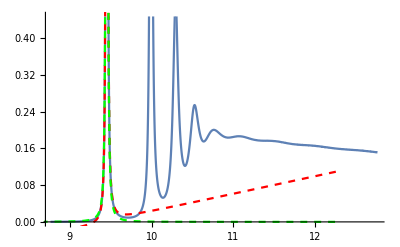

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[bbdata[i],Joined->True],Plot[BW[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],dfitbb[[i,ii]],cfitbb[[i,ii]],sfitbb[[i,ii]],s2fitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],cfitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

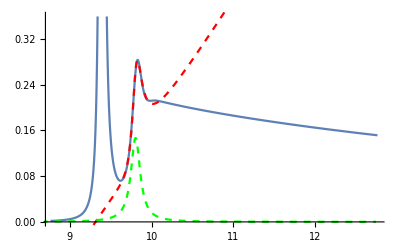

```mathematica
Block[{i=14,ii=2},Show[{ListPlot[bbdatau[i],Joined->True],Plot[BW[x,wrfitbbu[[i,ii]],gfitbbu[[i,ii]],dfitbbu[[i,ii]],cfitbbu[[i,ii]],sfitbbu[[i,ii]],s2fitbbu[[i,ii]]],{x,0.7wrfitbbu[[i,ii]],1.3wrfitbbu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbu[[i,ii]],gfitbbu[[i,ii]],cfitbbu[[i,ii]]],{x,0.7wrfitbbu[[i,ii]],1.3wrfitbbu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

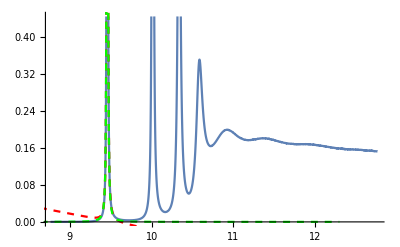

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[bbdatal[i],Joined->True],Plot[BW[x,wrfitbbl[[i,ii]],gfitbbl[[i,ii]],dfitbbl[[i,ii]],cfitbbl[[i,ii]],sfitbbl[[i,ii]],s2fitbbl[[i,ii]]],{x,0.7wrfitbbl[[i,ii]],1.3wrfitbbl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbl[[i,ii]],gfitbbl[[i,ii]],cfitbbl[[i,ii]]],{x,0.7wrfitbbl[[i,ii]],1.3wrfitbbl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
bbcont={10.564,10.564,10.564,10.564,10.564,10.564,10.527378512103652,10.458038653777693,10.397063916534186,10.342760403792504,10.29387623752128,10.250287745552837,10.211257314210796,10.175007169917937,10.141170889585075,10.109446471184569,10.07958251011836,10.051367810758183,10.024623490811384,9.999196889701759,9.974956821724826,9.951789836385098,9.929597243764736,9.908292727055487,9.887800410385704,9.868053283010278,9.8489919048906,9.830563336162639,9.812720245805579,9.795420167737708,9.778624869170192,9.7622998219724,9.746413752113597,9.73093825028397,9.715847441594637,9.70111770262072,9.686727410977637,9.672656731880348,9.658887433115186,9.645402718265931,9.63218708567251,9.619226201757378,9.606506788016578,9.594016525065872,9.581743962309114,9.569678442002388,9.557810028829598,9.546129447587175,9.534628028433774,9.523297655326948,9.512130722755183,9.501120093237194,9.490259062395165,9.479541324029718,9.468960941472151,9.458512318802216,9.448190177148303,9.437989530790198,9.427905667463891,9.417934128355947,9.408070691658118,9.398311355730087,9.388652325240962,9.379089997009492,9.369620948139811,9.360241924193852,9.350949828844204,9.341741714067625,9.33261477101332,9.323566321819921,9.314593811663407,9.305694801731502,9.296866962370737,9.288108067010732,9.279415986240773,9.270788682513258,9.262224205031721,9.25372068509524,9.245276331681337,9.236889427344641,9.228558324368382,9.220281441169213,9.21205725890185,9.203884318318714,9.1957612167662,9.187686605405265,9.179659186592552,9.171677711386995,9.163740977233696,9.155847825771016,9.147997140763607};
```

```mathematica
bbcontl={10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.556402146981373,10.503936983412133,10.455835139224124,10.411477761546102,10.370361368192109,10.332071801428693,10.296264991329638,10.26265250686442,10.23099056738254,10.201071578737595,10.172717540135894,10.145774854348728,10.120110203200447,10.095607240464139,10.072163918306192,10.049690309142665,10.028106817698344,10.007342708340918,9.987334871080696,9.968026800578471,9.949367736063811,9.931311926239225,9.91381801205047,9.896848503330894,9.880369319718294,9.864349403123105,9.848760384960684,9.833576287975887,9.818773276924803,9.804329435992369,9.790224571303035,9.77644004558396,9.76295862200426,9.749764335171768,9.736842371333513,9.724178963211907,9.71176129874024,9.699577434361936,9.687616224367794,9.675867249744705,9.664320762129096,9.652967625688675,9.641799271821718,9.630807651566252,9.619985198648621,9.609324790160615,9.598819716333189,9.58846364769082,9.57825061025976,9.568174957947596,9.558231351983078,9.548414737794069,9.538720327482803,9.529143580844627,9.519680189814283,9.510326063345445,9.501077313150551,9.491930241730907,9.482881329700549,9.473927225737238,9.465064735601445,9.45629081364721,9.447602553265106,9.438997179579836,9.43047204128095,9.422024604095093,9.413652444011118,9.405353241216105,9.397124774626468,9.388964916189838,9.380871626430418,9.372842949299956,9.364877008230827,9.356972001856473,9.349126200182672,9.341337941115013,9.333605627015798,9.325927721542769,9.318302746671728};
```

```mathematica
bbcontu={10.564,10.564,10.496709125685154,10.41040794662987,10.337633833937968,10.274919916331227,10.219920822198269,10.170989204687158,10.126931373477472,10.086859310726215,10.050097360560876,10.016615070530863,9.985996970589452,9.957186147022338,9.929964888295984,9.904151009416548,9.879590709219405,9.856153099980235,9.833725977965171,9.81221250735083,9.791528597691705,9.771600809088815,9.752364664255818,9.733763277273395,9.71574623114793,9.698268652522948,9.68129044387949,9.66477564242028,9.648691881422007,9.633009936610458,9.617703338222139,9.602748043328436,9.588122154435315,9.57380567508403,9.559780300705437,9.546029237911522,9.5325370444614,9.519289491429872,9.506273442709718,9.493476746891298,9.480888144183908,9.4684971829228,9.45629414512749,9.444269981750228,9.432416253100905,9.420725077119878,9.409189082121562,9.397801364617534,9.386555451580739,9.3754452659016,9.364465095784983,9.353609566455654,9.342873614973602,9.332252467006796,9.321741615886365,9.311336803446888,9.301034002469885,9.290829400797941,9.280719386505075,9.270700534675603,9.260769594775983,9.25092347961544,9.241159254528009,9.231474128085397,9.221865442847887,9.212330667402375,9.202867388573843,9.193473304376335,9.184146217617442,9.174884029535338,9.165684734475159,9.156546414276063,9.14746723375977,9.138445435741774,9.129479337209272,9.120567324915452,9.111707852038192,9.102899434413285,9.094140647435934,9.085430123009214,9.076766546509512,9.068148654431594,9.059575231425,9.05104510838572,9.042557159848723,9.034110302084406,9.025703491145125,9.017335720869662,9.009006021208178,9.000713456559843,8.992457124206853};
```

```mathematica
bbbind=bbcont-wrfitbb;
bbbindu=bbcontu-wrfitbbu;
bbbindl=bbcontl-wrfitbbl;
```

```mathematica
Do[If[(bbbind-gfitbb)[[i,1]]>0,bb1Tmelt=i],{i,1,Length[bbbind]}];
Do[If[(bbbind-gfitbb)[[i,2]]>0,bb2Tmelt=i],{i,1,bb1Tcut}];
Do[If[(bbbind-gfitbb)[[i,3]]>0,bb3Tmelt=i],{i,1,bb2Tcut}];
Do[If[(bbbind-gfitbb)[[i,4]]>0,bb4Tmelt=i,bb4Tmelt=1],{i,1,bb3Tcut}];
```

```mathematica
Do[If[(bbbindu-gfitbbu)[[i,1]]>0,bb1uTmelt=i],{i,1,Length[bbbind]}];
Do[If[(bbbindu-gfitbbu)[[i,2]]>0,bb2uTmelt=i],{i,1,bb1uTcut}];
Do[If[(bbbindu-gfitbbu)[[i,3]]>0,bb3uTmelt=i,bb3uTmelt=1],{i,1,bb2uTcut}];
Do[If[(bbbindu-gfitbbu)[[i,4]]>0,bb4uTmelt=i,bb4uTmelt=1],{i,1,bb3uTcut}];
```

```mathematica
Do[If[(bbbindl-gfitbbl)[[i,1]]>0,bb1lTmelt=i+1],{i,1,Length[bbbind]}];
Do[If[(bbbindl-gfitbbl)[[i,2]]>0,bb2lTmelt=i+1],{i,1,bb1lTcut}];
Do[If[(bbbindl-gfitbbl)[[i,3]]>0,bb3lTmelt=i+1],{i,1,bb2lTcut}];
Do[If[(bbbindl-gfitbbl)[[i,4]]>0,bb4lTmelt=i+1],{i,1,bb3lTcut}];
```

```mathematica
N[{Tscanborig[[bb1lTmelt]],Tscanborig[[bb1Tmelt]],Tscanborig[[bb1uTmelt]]}/0.155]
```

{3.35484,2.83871,2.48387}

```mathematica
N[{Tscanborig[[bb2lTmelt]],Tscanborig[[bb2Tmelt]],Tscanborig[[bb2uTmelt]]}/0.155]
```

{1.93548,1.6129,1.3871}

```mathematica
N[{Tscanborig[[bb3lTmelt]],Tscanborig[[bb3Tmelt]],Tscanborig[[bb3uTmelt]]}/0.155]
```

{1.58065,1.29032,0.967742}

```mathematica
N[{Tscanborig[[bb4lTmelt]],Tscanborig[[bb4Tmelt]],Tscanborig[[bb4uTmelt]]}/0.155]
```

{1.3871,0.967742,0.967742}

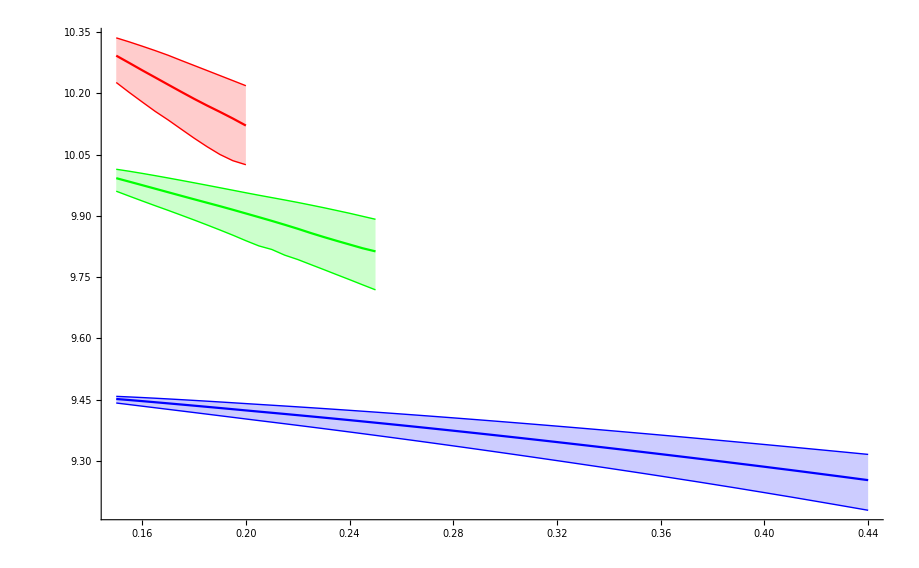

```mathematica
ListPlot[{Transpose[{Tscanborig[[;;bb1Tmelt]],wrfitbb[[;;bb1Tmelt,1]]}],Transpose[{Tscanborig[[;;bb1Tmelt]],wrfitbbl[[;;bb1Tmelt,1]]}],Transpose[{Tscanborig[[;;bb1Tmelt]],wrfitbbu[[;;bb1Tmelt,1]]}],Transpose[{Tscanborig[[;;bb2Tmelt]],wrfitbb[[;;bb2Tmelt,2]]}],Transpose[{Tscanborig[[;;bb2Tmelt]],wrfitbbl[[;;bb2Tmelt,2]]}],Transpose[{Tscanborig[[;;bb2Tmelt]],wrfitbbu[[;;bb2Tmelt,2]]}],Transpose[{Tscanborig[[;;bb3Tmelt]],wrfitbb[[;;bb3Tmelt,3]]}],Transpose[{Tscanborig[[;;bb3Tmelt]],wrfitbbl[[;;bb3Tmelt,3]]}],Transpose[{Tscanborig[[;;bb3Tmelt]],wrfitbbu[[;;bb3Tmelt,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```

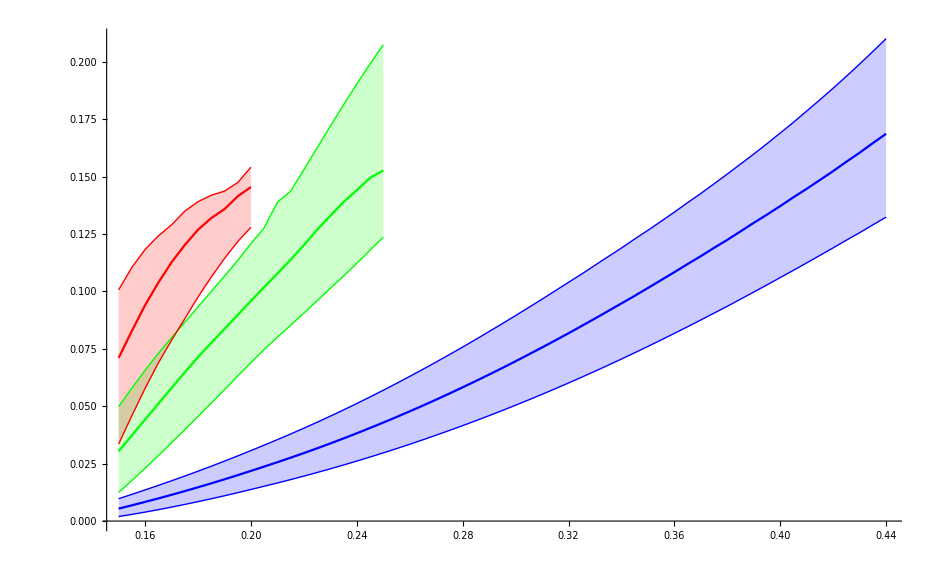

```mathematica
ListPlot[{Transpose[{Tscanborig[[;;bb1Tmelt]],gfitbb[[;;bb1Tmelt,1]]}],Transpose[{Tscanborig[[;;bb1Tmelt]],gfitbbl[[;;bb1Tmelt,1]]}],Transpose[{Tscanborig[[;;bb1Tmelt]],gfitbbu[[;;bb1Tmelt,1]]}],Transpose[{Tscanborig[[;;bb2Tmelt]],gfitbb[[;;bb2Tmelt,2]]}],Transpose[{Tscanborig[[;;bb2Tmelt]],gfitbbl[[;;bb2Tmelt,2]]}],Transpose[{Tscanborig[[;;bb2Tmelt]],Delete[gfitbbu,13][[;;bb2Tmelt,2]]}],Transpose[{Tscanborig[[;;bb3Tmelt]],gfitbb[[;;bb3Tmelt,3]]}],Transpose[{Tscanborig[[;;bb3Tmelt]],gfitbbl[[;;bb3Tmelt,3]]}],Transpose[{Tscanborig[[;;bb3Tmelt]],gfitbbu[[;;bb3Tmelt,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```

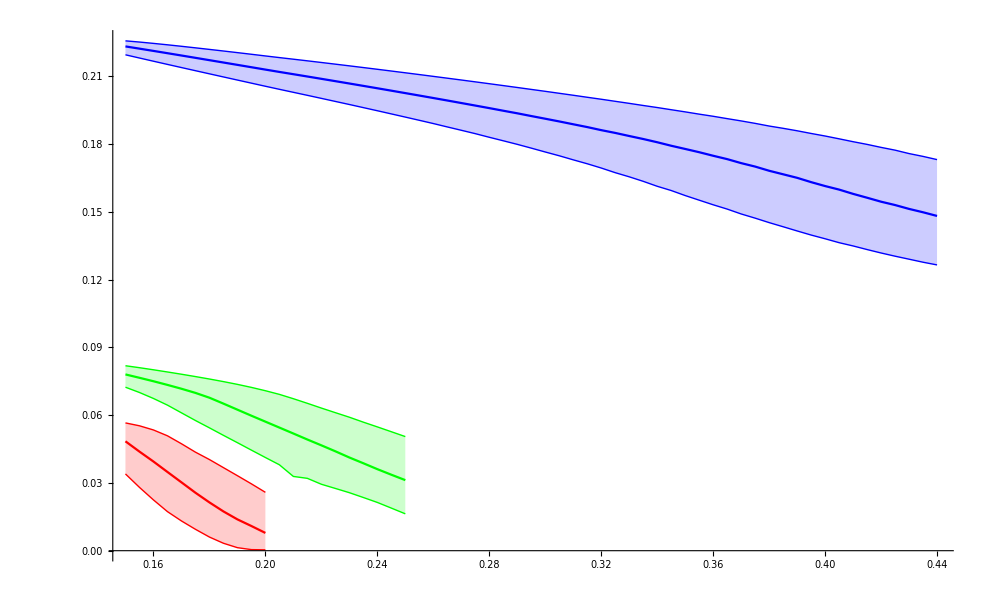

```mathematica
ListPlot[{Transpose[{Tscanborig[[;;bb1Tmelt]],areafitbb[[;;bb1Tmelt,1]]}],Transpose[{Tscanborig[[;;bb1Tmelt]],areafitbbl[[;;bb1Tmelt,1]]}],Transpose[{Tscanborig[[;;bb1Tmelt]],areafitbbu[[;;bb1Tmelt,1]]}],Transpose[{Tscanborig[[;;bb2Tmelt]],areafitbb[[;;bb2Tmelt,2]]}],Transpose[{Tscanborig[[;;bb2Tmelt]],areafitbbl[[;;bb2Tmelt,2]]}],Transpose[{Tscanborig[[;;bb2Tmelt]],areafitbbu[[;;bb2Tmelt,2]]}],Transpose[{Tscanborig[[;;bb3Tmelt]],areafitbb[[;;bb3Tmelt,3]]}],Transpose[{Tscanborig[[;;bb3Tmelt]],areafitbbl[[;;bb3Tmelt,3]]}],Transpose[{Tscanborig[[;;bb3Tmelt]],areafitbbu[[;;bb3Tmelt,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```

## Bottomonium p-wave

#### New fitting function

```mathematica
fit[input_,output_,Tscan_]:=Module[{temp=Range[1,Length[Tscan]],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],minx+a≤x≤minx+2 a},{x,minx+3a/2}],maxxy/30],FindArgMax[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}][[1]]},{a,1,1/2(maxx-minx),1/50}],First][[All,2]]]];bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2]},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];,{ii,Length[Tscan]}];output=temp;];
```

### Input data

```mathematica
Tscanborig=Join[Table[i,{i,0.15,0.16,0.001}],Table[i,{i,0.162,0.3,0.003}]]
```

{0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249,0.252,0.255,0.258,0.261,0.264,0.267,0.27,0.273,0.276,0.279,0.282,0.285,0.288,0.291,0.294,0.297,0.3}

```mathematica
Do[bbdata[n]=Import["bb/pwbbT"<>ToString[Round[1000 Tscanborig[[n]]]]<>"spectra.dat"]/.{a_,b_}:>{a,b/a^2};,{n,Length[Tscanborig]}];
```

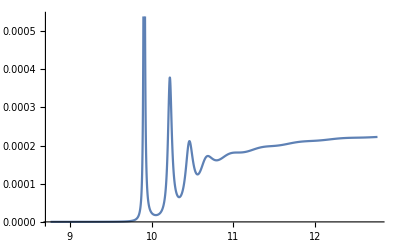

```mathematica
Block[{n=1},ListPlot[bbdata[n],Joined->True]]
```

```mathematica
Do[bbdatal[n]=Import["bb/pwbbT"<>ToString[Round[1000 Tscanborig[[n]]]]<>"lspectra.dat"]/.{a_,b_}:>{a,b/a^2};,{n,Length[Tscanborig]}];
```

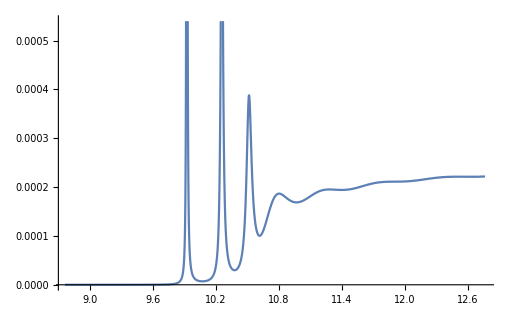

```mathematica
Block[{n=1},ListPlot[bbdatal[n],Joined->True]]
```

```mathematica
Do[bbdatau[n]=Import["bb/pwbbT"<>ToString[Round[1000 Tscanborig[[n]]]]<>"uspectra.dat"]/.{a_,b_}:>{a,b/a^2};,{n,Length[Tscanborig]}];
```

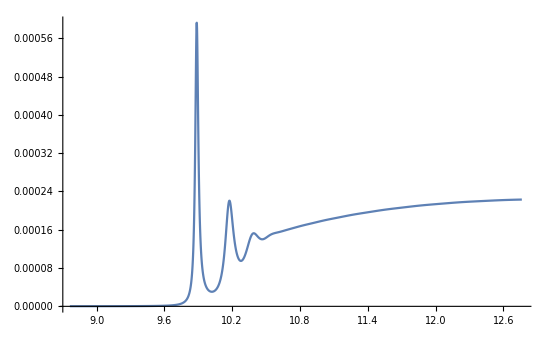

```mathematica
Block[{n=1},ListPlot[bbdatau[n],Joined->True]]
```

### Fitting

```mathematica
Clear[bbmodel,bbmodelu,bbmodell]
fit[bbdata,bbmodel,Tscanborig];
fit[bbdatau,bbmodelu,Tscanborig];
fit[bbdatal,bbmodell,Tscanborig];
```

### Store Results

```mathematica
Do[If[Length[bbmodel[[i]]]>4,bbmodel[[i]]=bbmodel[[i,;;4]]];If[Length[bbmodelu[[i]]]>4,bbmodelu[[i]]=bbmodelu[[i,;;4]]];If[Length[bbmodell[[i]]]>4,bbmodell[[i]]=bbmodell[[i,;;4]]];,{i,Length[bbmodel]}];
```

```mathematica
Clear[wrfitbb,wrfitbbl,wrfitbbu,gfitbb,gfitbbl,gfitbbu,areafitbb,areafitbbu,areafitbbl,cfitbb,cfitbbl,cfitbbu,dfitbb,dfitbbl,dfitbbu,sfitbb,sfitbbl,sfitbbu,s2fitbb,s2fitbbl,s2fitbbu];
store[wr,wrfitbb,bbmodel];
store[wr,wrfitbbl,bbmodell];
store[wr,wrfitbbu,bbmodelu];
store[Γ,gfitbb,bbmodel];
store[Γ,gfitbbl,bbmodell];
store[Γ,gfitbbu,bbmodelu];
store[const,cfitbb,bbmodel];
store[const,cfitbbl,bbmodell];
store[const,cfitbbu,bbmodelu];
store[δbg,dfitbb,bbmodel];
store[δbg,dfitbbl,bbmodell];
store[δbg,dfitbbu,bbmodelu];
store[shift,sfitbb,bbmodel];
store[shift,sfitbbl,bbmodell];
store[shift,sfitbbu,bbmodelu];
store[shift2,s2fitbb,bbmodel];
store[shift2,s2fitbbl,bbmodell];
store[shift2,s2fitbbu,bbmodelu];
storearea[areafitbb,bbmodel];
storearea[areafitbbl,bbmodell];
storearea[areafitbbu,bbmodelu];
```

### Display Results

```mathematica
import[wrfitbb];
import[wrfitbbl];
import[wrfitbbu];
import[gfitbb];
import[gfitbbl];
import[gfitbbu];
import[cfitbb];
import[cfitbbl];
import[cfitbbu];
import[dfitbb];
import[dfitbbl];
import[dfitbbu];
import[sfitbb];
import[sfitbbl];
import[sfitbbu];
import[s2fitbb];
import[s2fitbbl];
import[s2fitbbu];
import[areafitbb];
import[areafitbbl];
import[areafitbbu];
```

```mathematica
Do[If[Length[wrfitbb[[-i]]]<2,bb1Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];
Do[If[Length[wrfitbbu[[-i]]]<2,bb1uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];
Do[If[Length[wrfitbbl[[-i]]]<2,bb1lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
Do[If[Length[wrfitbb[[-i]]]<3,bb2Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];
Do[If[Length[wrfitbbu[[-i]]]<3,bb2uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];
Do[If[Length[wrfitbbl[[-i]]]<3,bb2lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
Do[If[Length[wrfitbb[[-i]]]<4,bb3Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];Do[If[Length[wrfitbbu[[-i]]]<4,bb3uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];Do[If[Length[wrfitbbl[[-i]]]<4,bb3lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
```

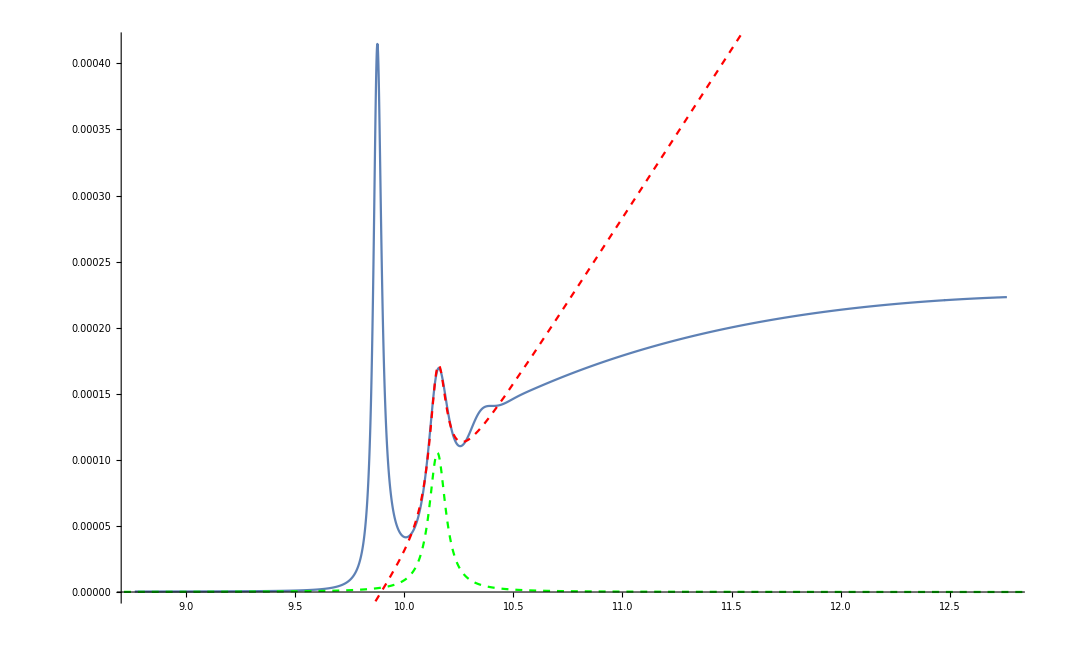

```mathematica
Block[{i=17,ii=2},Show[{ListPlot[bbdata[i],Joined->True],Plot[BW[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],dfitbb[[i,ii]],cfitbb[[i,ii]],sfitbb[[i,ii]],s2fitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],cfitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

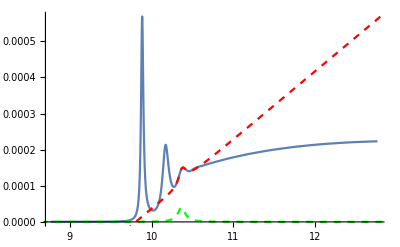

```mathematica
Block[{i=2,ii=3},Show[{ListPlot[bbdatau[i],Joined->True],Plot[BW[x,wrfitbbu[[i,ii]],gfitbbu[[i,ii]],dfitbbu[[i,ii]],cfitbbu[[i,ii]],sfitbbu[[i,ii]],s2fitbbu[[i,ii]]],{x,0.7wrfitbbu[[i,ii]],1.3wrfitbbu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbu[[i,ii]],gfitbbu[[i,ii]],cfitbbu[[i,ii]]],{x,0.7wrfitbbu[[i,ii]],1.3wrfitbbu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

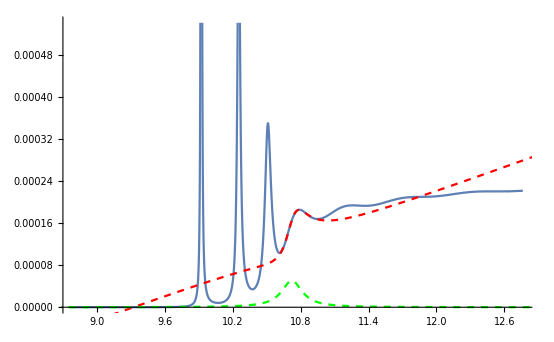

```mathematica
Block[{i=3,ii=4},Show[{ListPlot[bbdatal[i],Joined->True],Plot[BW[x,wrfitbbl[[i,ii]],gfitbbl[[i,ii]],dfitbbl[[i,ii]],cfitbbl[[i,ii]],sfitbbl[[i,ii]],s2fitbbl[[i,ii]]],{x,0.7wrfitbbl[[i,ii]],1.3wrfitbbl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbl[[i,ii]],gfitbbl[[i,ii]],cfitbbl[[i,ii]]],{x,0.7wrfitbbl[[i,ii]],1.3wrfitbbl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
n=2;
input[n]=bbdatal[n];
```

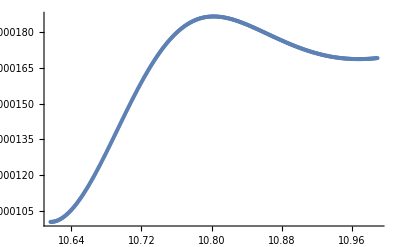

```mathematica
ListPlot[inputc[[4]]]
```

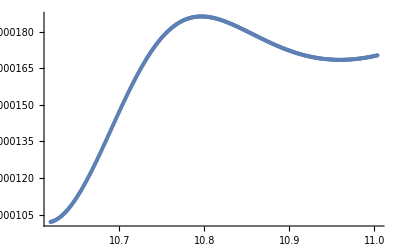

```mathematica
ListPlot[inputc[[3,250;;-220]],PlotRange->All]
```

```mathematica
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],minx+a≤x≤minx+2 a},{x,minx+3a/2}],maxxy/30],FindArgMax[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}][[1]]},{a,1,1/2(maxx-minx),1/50}],First][[All,2]]]];bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
```

```mathematica
bbmodell[[1,4]]["BestFitParameters"]
```

{wr→10.7338,Γ→0.236968,const→0.0000580554,δbg→0.0000620407,shift→0.0000936317,shift2→0.000109694}

```mathematica
temp=NonlinearModelFit[inputc[[3,250;;-220]],{BW[w,wr,Γ,δbg,const,shift,shift2]},{{wr,10.733780504604958},{Γ,0.23696756314259557},{const,0.00005805538317798994},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000]
```

FittedModel[0.000104488+(9.67915×10^-7)/(0.0139985+(-10.741+w)^2)+0.000134339 (-10.741+w)+(5.46929×10^-6 (-10.741+w))/(0.0139985+(-10.741+w)^2)]

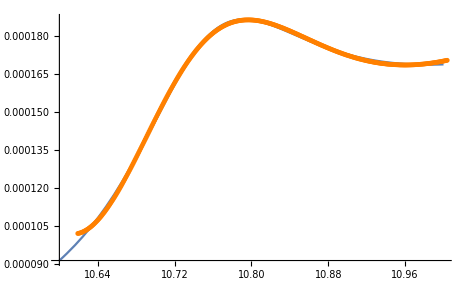

```mathematica
Show[Plot[temp[x],{x,10.6,11}],ListPlot[inputc[[3,250;;-220]],PlotStyle->{Orange,Dashed}]]
```

```mathematica
bbmodell[[2]]=Append[bbmodell[[2]],temp]
```

{FittedModel[1.46694×10^-6+(4.55676×10^-8)/(0.000016622+(-9.92394+w)^2)+6.82267×10^-6 (-9.92394+w)+(2.44078×10^-7 (-9.92394+w))/(0.000016622+(-9.92394+w)^2)],FittedModel[7.26488×10^-6+(1.50235×10^-7)/(0.00017498+(-10.2555+w)^2)+0.0000313606 (-10.2555+w)+(5.87401×10^-7 (-10.2555+w))/(0.00017498+(-10.2555+w)^2)],FittedModel[0.0000443142+(2.72579×10^-7)/(0.000836614+(-10.5125+w)^2)+0.000253736 (-10.5125+w)+(9.43452×10^-7 (-10.5125+w))/(0.000836614+(-10.5125+w)^2)],FittedModel[0.000104488+(9.67915×10^-7)/(0.0139985+(-10.741+w)^2)+0.000134339 (-10.741+w)+(5.46929×10^-6 (-10.741+w))/(0.0139985+(-10.741+w)^2)]}

```mathematica
bbcont={10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.527378512103652,10.48465676411899,10.44523651269,10.408678409753676,10.374620214914984,10.342760403792504,10.312845805961425,10.28466215987651,10.258465302605183,10.23431528929649,10.211257314210796,10.189198662206424,10.16805729728462,10.147760337068178,10.128242785457232,10.109446471184569,10.091319155085763,10.073813775501225,10.056887807078887,10.040502716143385,10.024623490811384,10.009218232516773,9.994257817920584,9.97971558775915,9.965567086223086,9.951789836385098,9.938363130361983,9.925267861458286,9.91248636297944,9.900002271971234,9.887800410385704,9.87586667114882,9.8641879289901,9.852751947397785,9.84154730782897,9.830563336162639,9.819790043731144,9.809218070104144,9.798838634336326,9.788643485665855,9.778624869170192};
```

```mathematica
bbcontl={10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.556402146981373,10.52436017602119,10.493989268327525,10.465138001767468,10.437673313594308,10.411477761546102,10.386447264050156,10.362489224356327,10.33952096383713,10.317468411317149,10.296264991329638,10.275850673873647,10.256171191971559,10.237177339449303,10.218824386101536,10.201071578737595,10.183881685376406,10.167220629235924,10.151057145617616,10.135362493019231,10.120110203200447,10.105275846077447,10.090836844624137,10.076772286686154,10.06306278071079,10.049690309142665,10.036638110709914,10.023890567758505,10.011433110625022,9.999252122197767,9.987334871080696};
```

```mathematica
bbcontu={10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.557098734886699,10.536127561736603,10.516018030246517,10.496709125685154,10.46027738140197,10.410407946629869,10.365373368647996,10.324374028670963,10.286782512484121,10.252099170904762,10.219920822198269,10.18991826646113,10.161819839655408,10.13539919326147,10.110466079263173,10.086859310726215,10.06444131931456,10.043093901018867,10.022977759721616,10.004135281949424,9.985996970589452,9.968508422126757,9.951621020808282,9.935291168039978,9.919479634246828,9.904151009416548,9.889273235724392,9.87481720820814,9.860756431944163,9.847066728134983,9.833725977965171,9.820713897768155,9.808011851930662,9.795602678581826,9.783470542785476,9.771600809088815,9.759979921356909,9.748595306143025,9.737435279173528,9.726488965804181,9.71574623114793,9.705197612846757,9.694834267852919,9.684647917020023,9.674630802285819,9.66477564242028,9.655075597028159,9.645524231684183,9.636115487885295,9.626843652970937,9.617703338222139};
```

```mathematica
bbbind=bbcont-wrfitbb;
bbbindu=bbcontu-wrfitbbu;
bbbindl=bbcontl-wrfitbbl;
```

```mathematica
Do[If[(bbbind-gfitbb)[[i,1]]>0,bb1Tmelt=i],{i,1,Length[bbbind]}];
Do[If[(bbbind-gfitbb)[[i,2]]>0,bb2Tmelt=i],{i,1,bb1Tcut}];
Do[If[(bbbind-gfitbb)[[i,3]]>0,bb3Tmelt=i],{i,1,bb2Tcut}];
Do[If[(bbbind-gfitbb)[[i,4]]>0,bb4Tmelt=i,bb4Tmelt=1],{i,1,bb3Tcut}];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Do[If[(bbbindu-gfitbbu)[[i,1]]>0,bb1uTmelt=i],{i,1,Length[bbbind]}];
Do[If[(bbbindu-gfitbbu)[[i,2]]>0,bb2uTmelt=i],{i,1,bb1uTcut}];
Do[If[(bbbindu-gfitbbu)[[i,3]]>0,bb3uTmelt=i,bb3uTmelt=1],{i,1,bb2uTcut}];
bb4uTmelt=1;
Do[If[(bbbindu-gfitbbu)[[i,4]]>0,bb4uTmelt=i],{i,1,bb3uTcut}];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Do[If[(bbbindl-gfitbbl)[[i,1]]>0,bb1lTmelt=i],{i,1,Length[bbbind]}];
Do[If[(bbbindl-gfitbbl)[[i,2]]>0,bb2lTmelt=i],{i,1,bb1lTcut}];
Do[If[(bbbindl-gfitbbl)[[i,3]]>0,bb3lTmelt=i],{i,1,bb2lTcut}];
Do[If[(bbbindl-gfitbbl)[[i,4]]>0,bb4lTmelt=i,bb4lTmelt=1],{i,1,bb3lTcut}];
```

```mathematica
N[{Tscanborig[[bb1lTmelt-1]],Tscanborig[[bb1Tmelt]],Tscanborig[[bb1uTmelt]]}/0.155]
```

{1.93548,1.70323,1.4129}

```mathematica
N[{Tscanborig[[bb2lTmelt]],Tscanborig[[bb2Tmelt]],Tscanborig[[bb2uTmelt]]}/0.155]
```

{1.5871,1.35484,1.2}

```mathematica
N[{Tscanborig[[bb3lTmelt]],Tscanborig[[bb3Tmelt]],Tscanborig[[bb3uTmelt]]}/0.155]
```

{1.18065,1.03226,0.974194}

```mathematica
N[{Tscanborig[[bb4lTmelt]],Tscanborig[[bb4Tmelt]],Tscanborig[[bb4uTmelt]]}/0.155]
```

{0.967742,0.967742,0.967742}

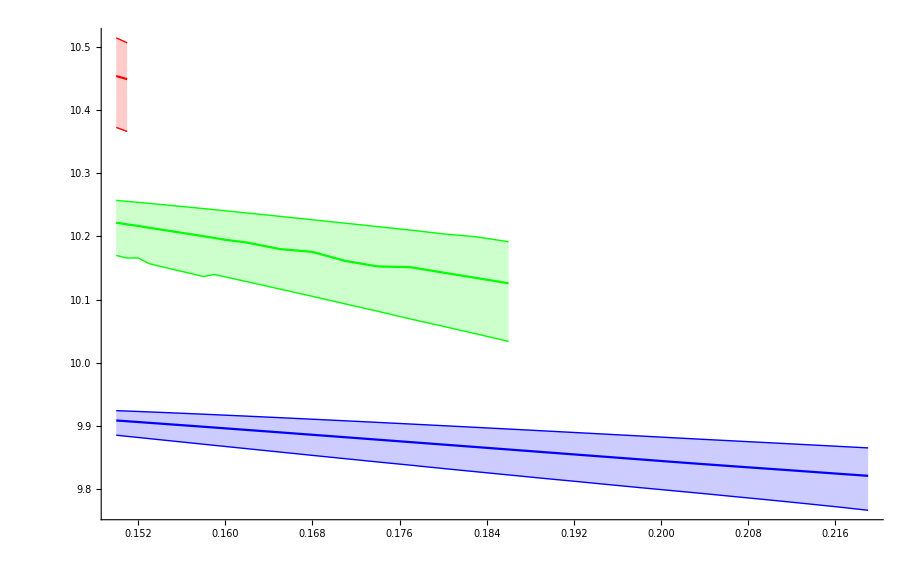

```mathematica
ListPlot[{Transpose[{Tscanborig[[;;bb1uTmelt]],wrfitbb[[;;bb1uTmelt,1]]}],Transpose[{Tscanborig[[;;bb1uTmelt]],wrfitbbl[[;;bb1uTmelt,1]]}],Transpose[{Tscanborig[[;;bb1uTmelt]],wrfitbbu[[;;bb1uTmelt,1]]}],Transpose[{Tscanborig[[;;bb2uTmelt]],wrfitbb[[;;bb2uTmelt,2]]}],Transpose[{Tscanborig[[;;bb2uTmelt]],wrfitbbl[[;;bb2uTmelt,2]]}],Transpose[{Tscanborig[[;;bb2uTmelt]],wrfitbbu[[;;bb2uTmelt,2]]}],Transpose[{Tscanborig[[;;bb3uTmelt]],wrfitbb[[;;bb3uTmelt,3]]}],Transpose[{Tscanborig[[;;bb3uTmelt]],wrfitbbl[[;;bb3uTmelt,3]]}],Transpose[{Tscanborig[[;;bb3uTmelt]],wrfitbbu[[;;bb3uTmelt,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```

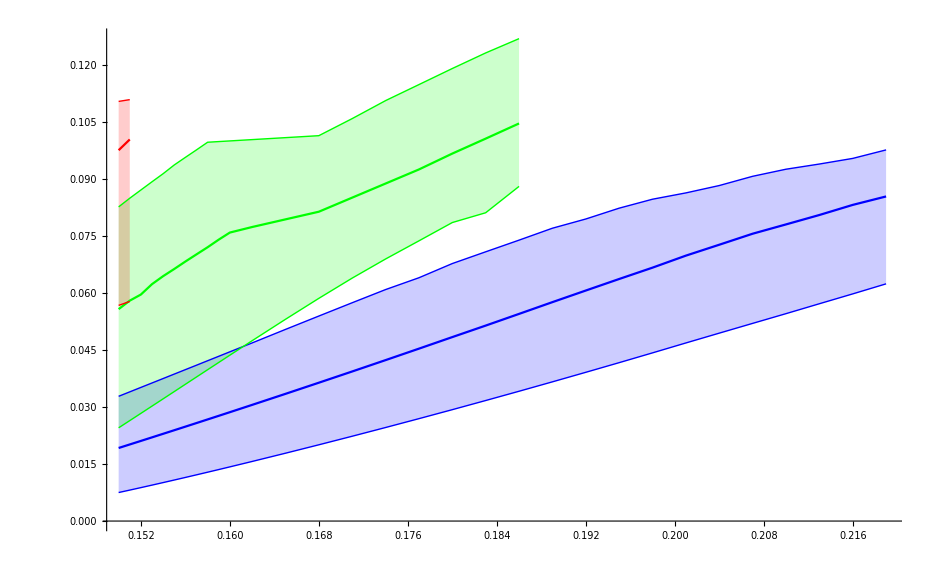

```mathematica
ListPlot[{Transpose[{Tscanborig[[;;bb1uTmelt]],gfitbb[[;;bb1uTmelt,1]]}],Transpose[{Tscanborig[[;;bb1uTmelt]],gfitbbl[[;;bb1uTmelt,1]]}],Transpose[{Tscanborig[[;;bb1uTmelt]],gfitbbu[[;;bb1uTmelt,1]]}],Transpose[{Delete[Tscanborig[[;;bb2uTmelt]],{{13},{15},{16}}],Delete[gfitbb[[;;bb2uTmelt,2]],{{13},{15},{16}}]}],Transpose[{Tscanborig[[;;bb2uTmelt]],gfitbbl[[;;bb2uTmelt,2]]}],Transpose[{Delete[Tscanborig[[;;bb2uTmelt]],{{3},{10},{11},{12},{13}}],Delete[gfitbbu[[;;bb2uTmelt,2]],{{3},{10},{11},{12},{13}}]}],Transpose[{Tscanborig[[;;bb3uTmelt]],gfitbb[[;;bb3uTmelt,3]]}],Transpose[{Tscanborig[[;;bb3uTmelt]],gfitbbl[[;;bb3uTmelt,3]]}],Transpose[{Tscanborig[[;;bb3uTmelt]],gfitbbu[[;;bb3uTmelt,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```

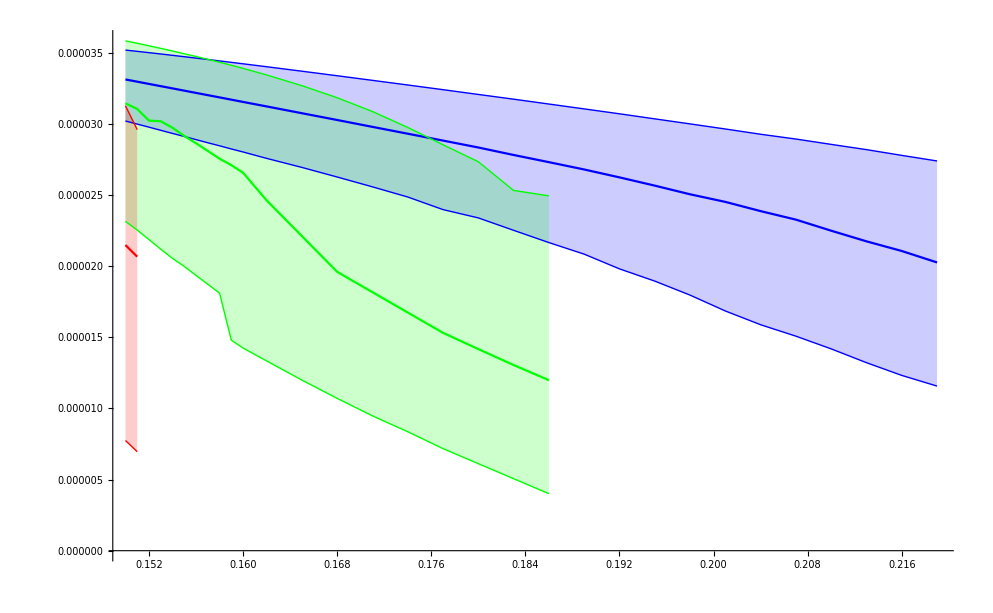

```mathematica
ListPlot[{Transpose[{Tscanborig[[;;bb1uTmelt]],areafitbb[[;;bb1uTmelt,1]]}],Transpose[{Tscanborig[[;;bb1uTmelt]],areafitbbl[[;;bb1uTmelt,1]]}],Transpose[{Tscanborig[[;;bb1uTmelt]],areafitbbu[[;;bb1uTmelt,1]]}],Transpose[{Delete[Tscanborig[[;;bb2uTmelt]],{{13},{15},{16}}],Delete[areafitbb[[;;bb2uTmelt,2]],{{13},{15},{16}}]}],Transpose[{Tscanborig[[;;bb2uTmelt]],areafitbbl[[;;bb2uTmelt,2]]}],Transpose[{Delete[Tscanborig[[;;bb2uTmelt]],{3}],Delete[areafitbbu[[;;bb2uTmelt,2]],{3}]}],Transpose[{Tscanborig[[;;bb3uTmelt]],areafitbb[[;;bb3uTmelt,3]]}],Transpose[{Tscanborig[[;;bb3uTmelt]],areafitbbl[[;;bb3uTmelt,3]]}],Transpose[{Tscanborig[[;;bb3uTmelt]],areafitbbu[[;;bb3uTmelt,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```